# Testing singleSlipPlaneSolution.yaml with Dislocation Density Hardening

In this notebook, we examine slip along a plane that is rotated to the global axes.

<!-- =========================================================================================== -->

     <ParameterList name=”Materials”>

          <ParameterList name=”metal_fcc”>


<!-- ~~~~~~~~~ Specify material model ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->

               <ParameterList name=”Material Model”>

                    <Parameter name=”Model Name”
                               type=”string”
                               value=”CrystalPlasticity”/>

               </ParameterList>


<!-- ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->
<!-- ~~~~~~~~~ Set program controls ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->
<!-- ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->

               <Parameter name=”Integration Scheme”
                          type=”string”
                          value=”Implicit”/>

               <Parameter name=”Implicit Integration Relative Tolerance”
                          type=”double”
                          value=”1.0*10^-35”/>

               <Parameter name=”Implicit Integration Absolute Tolerance”
                          type=”double”
                          value=”1.0*10^-10”/>

               <Parameter name=”Implicit Integration Max Iterations”
                          type=”int”
                          value=”100”/>

       <ParameterList name=”Crystal Elasticity”>

                    <Parameter name=”C11”
                               type=”double”
                               value=”204.6e3”/>

                    <Parameter name=”C12”
                               type=”double”
                               value=”137.7e3”/>

                    <Parameter name=”C44”
                               type=”double”
                               value=”126.2e3”/>

                    <Parameter name=”Basis Vector 1”
                               type=”Array(double)”
                               value=”{-0.09175170953613698, | 0.908248290463863, | 0.408248290463863}”/>

                    <Parameter name=”Basis Vector 2”
                               type=”Array(double)”
                               value=”{0.908248290463863, | -0.09175170953613698, | 0.408248290463863}”/>

                    <Parameter name=”Basis Vector 3”
                               type=”Array(double)”
                               value=”{0.408248290463863, | 0.408248290463863, | -0.816496580927726}”/>

               </ParameterList>
               
<!-- ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->
<!-- ~~~~~~~~~ Set crystal plasticity parameters ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->
<!-- ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->

               <Parameter name=”Number of Slip Systems”
                          type=”int”
                         value=”1”/>

<!-- ~~~~~~~~~ Specify slip system 1 ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->

               <ParameterList name=”Slip System 1”>

                    <Parameter name=”Slip Direction”
                               type=”Array(double)”
                               value=”{-1.0, 1.0, 0.0}”/>

                    <Parameter name=”Slip Normal”
                               type=”Array(double)”
                               value=”{1.0, 1.0, 1.0}”/>

                    <Parameter name=”Tau Critical”
                               type=”double”
                               value=”122.0”/>

                    <Parameter name=”Gamma Dot”
                               type=”double”
                               value=”1.0”/>

                    <Parameter name=”Gamma Exponent”
                               type=”double”
                               value=”50.0”/>

                    <Parameter name=”Hardening”
                               type=”double”
                               value=”0.0”/>

                    <Parameter name=”Hardening Exponent”
                               type=”double”
                               value=”0.0”/>

               </ParameterList>       
               
      
      
      Hardening Law: 
          Type: Dislocation Density
          Geometric Factor: 0.40000000
          Initial Hardening State: 80.00000000
          Generation Factor: 5000.00000000
          Annihilation Factor: 500.00000000
          Shear Modulus: 70700.00000000
          Burgers Vector Magnitude: 0.00028700
          
#        Units of Initial Hardening State must be consistent with units of Burgers Vector Magnitude - 1/m^2: 8e13, 1/mm^2: 8e7, 1/um^2: 8e1
#        Units of Shear Modulus must be consistent with units of elastic constants C11, C12, C44 - N/mm^2 (MPa): 7.07e+04
#        Units of Burgers Vector Magnitude must be consistent with units of Initial Hardening State - m:  2.87e-10, mm: 2.87e-7, um: 2.87e-4

## State basis for material coordinate system

Looking at a basis derived to simplify Schmid tensor and E3 (for debugging)

```mathematica
basis = {{1,0,0},{0,1/Sqrt[2],1/Sqrt[2]},{0,-1/Sqrt[2],1/Sqrt[2]}};
(*basis = {{1,0,0},{0,1,0},{0,0,1}};*)
MatrixForm[basis];
MatrixForm[N[basis,16]]
checkBasis = Norm[Simplify[basis . Transpose[basis]-IdentityMatrix[3]]];
checkDot12 = Simplify[basis[[1,All]] . basis[[2,All]]];
checkDot13 = Simplify[basis[[1,All]] . basis[[3,All]]];
checkDot23 = Simplify[basis[[2,All]] . basis[[3,All]]];
checkCross12= Norm[Simplify[Cross[basis[[1,All]],basis[[2,All]]]-basis[[3,All]]]];
checkCross23 = Norm[Simplify[Cross[basis[[2,All]],basis[[3,All]]]-basis[[1,All]]]];
checkCross31 = Norm[Simplify[Cross[basis[[3,All]],basis[[1,All]]]-basis[[2,All]]]];
checkDet=Det[basis]-1;
```

(1. | 0 | 0
0 | 0.7071067811865475 | 0.7071067811865475
0 | -0.7071067811865475 | 0.7071067811865475)

## Derive direction cosine matrix for coordinate transformations

```mathematica
orientation = Transpose[basis];
MatrixForm[orientation]
```

(1 | 0 | 0
0 | 1/(√2) | -1/(√2)
0 | 1/(√2) | 1/(√2))

## Transform slip and normal directions to global coordinate system

```mathematica
slipdirectionGlobal = Simplify[orientation . {{-1/Sqrt[2]},{1/Sqrt[2]},{0}}];
slipnormalGlobal = Simplify[orientation . {{1/Sqrt[3]},{1/Sqrt[3]},{1/Sqrt[3]}}];
MatrixForm[slipdirectionGlobal];
MatrixForm[slipnormalGlobal];
```

## Create Schmid tensor

```mathematica
P = Table[i*j*k*0,{i,1,12},{j,1,3},{k,1,3}];
n = Table[i*j*0,{i,1,12},{j,1,3}];
s = Table[i*j*0,{i,1,12},{j,1,3}];
T = Table[i*j*0,{i,1,12},{j,1,3}];
Psymm = Table[i*j*k*0,{i,1,12},{j,1,3},{k,1,3}];
latentMatrix = Table[i*j*0,{i,1,12},{j,1,12}];
auxMatrix = Table[i*j*0,{i,1,12},{j,1,12}];
R = orientation;
(*R = {{1,0,0},{0,1,0},{0,0,1}};*)
s[[1]] = R.{-1/Sqrt[2],1/Sqrt[2],0};
s[[2]] = R.{0,-1/Sqrt[2],1/Sqrt[2]};
s[[3]] = R.{1/Sqrt[2],0,-1/Sqrt[2]};
s[[4]] = R.{-1/Sqrt[2],-1/Sqrt[2],0};
s[[5]] = R.{1/Sqrt[2],0,1/Sqrt[2]};
s[[6]] = R.{0,1/Sqrt[2],-1/Sqrt[2]};
s[[7]] = R.{1/Sqrt[2],-1/Sqrt[2],0};
s[[8]] = R.{0,1/Sqrt[2],1/Sqrt[2]};
s[[9]] = R.{-1/Sqrt[2],0,-1/Sqrt[2]};
s[[10]] = R.{1/Sqrt[2],1/Sqrt[2],0};
s[[11]] = R.{-1/Sqrt[2],0,1/Sqrt[2]};
s[[12]] = R.{0,-1/Sqrt[2],-1/Sqrt[2]};

n[[1]] = R.{1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]};
n[[2]] = R.{1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]};
n[[3]] = R.{1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]};
n[[4]] = R.{-1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]};
n[[5]] = R.{-1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]};
n[[6]] = R.{-1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]};
n[[7]] = R.{-1/Sqrt[3],-1/Sqrt[3],1/Sqrt[3]};
n[[8]] = R.{-1/Sqrt[3],-1/Sqrt[3],1/Sqrt[3]};
n[[9]] = R.{-1/Sqrt[3],-1/Sqrt[3],1/Sqrt[3]};
n[[10]] = R.{1/Sqrt[3],-1/Sqrt[3],1/Sqrt[3]};
n[[11]] = R.{1/Sqrt[3],-1/Sqrt[3],1/Sqrt[3]};
n[[12]] = R.{1/Sqrt[3],-1/Sqrt[3],1/Sqrt[3]};

P[[1]] = Outer[Times,R.{-1/Sqrt[2],1/Sqrt[2],0},R.{1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]}];
P[[2]] = Outer[Times,R.{0,-1/Sqrt[2],1/Sqrt[2]},R.{1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]}];
P[[3]] = Outer[Times,R.{1/Sqrt[2],0,-1/Sqrt[2]},R.{1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]}];
P[[4]] = Outer[Times,R.{-1/Sqrt[2],-1/Sqrt[2],0},R.{-1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]}];
P[[5]] = Outer[Times,R.{1/Sqrt[2],0,1/Sqrt[2]},R.{-1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]}];
P[[6]] = Outer[Times,R.{0,1/Sqrt[2],-1/Sqrt[2]},R.{-1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]}];
P[[7]]= Outer[Times,R.{1/Sqrt[2],-1/Sqrt[2],0},R.{-1/Sqrt[3],-1/Sqrt[3],1/Sqrt[3]}];
P[[8]] = Outer[Times,R.{0,1/Sqrt[2],1/Sqrt[2]},R.{-1/Sqrt[3],-1/Sqrt[3],1/Sqrt[3]}];
P[[9]]= Outer[Times,R.{-1/Sqrt[2],0,-1/Sqrt[2]},R.{-1/Sqrt[3],-1/Sqrt[3],1/Sqrt[3]}];
P[[10]] = Outer[Times,R.{1/Sqrt[2],1/Sqrt[2],0},R.{1/Sqrt[3],-1/Sqrt[3],1/Sqrt[3]}];
P[[11]] = Outer[Times,R.{-1/Sqrt[2],0,1/Sqrt[2]},R.{1/Sqrt[3],-1/Sqrt[3],1/Sqrt[3]}];
P[[12]]= Outer[Times,R.{0,-1/Sqrt[2],-1/Sqrt[2]},R.{1/Sqrt[3],-1/Sqrt[3],1/Sqrt[3]}];

Do[
P[[i]] = Outer[Times,s[[i]],n[[i]]];
T[[i]] = Normalize[Cross[n[[i]],s[[i]]]];
,{i,1,12}
]

Do[
Do[
latentMatrix[[i,j]] = Abs[Dot[n[[i]],T[[j]]]];
auxMatrix[[i,j]] = Sqrt[1 - latentMatrix[[i,j]]^2];
,{j,1,12}],{i,1,12}
]

activeLatent = latentMatrix;

forest = activeLatent.{ρ,ρ0,ρ,ρ,ρ,ρ0,ρ0,ρ0,ρ0,ρ0,ρ0,ρ0};
parallel = auxMatrix.{ρ,ρ0,ρ,ρ,ρ,ρ0,ρ0,ρ0,ρ0,ρ0,ρ0,ρ0};

(*Print[MatrixForm[forest]];
Print[MatrixForm[parallel]];*)

LPfactor = Outer[Times,s[[1]], n[[1]]] -  Outer[Times,s[[3]], n[[3]]] - Outer[Times,s[[4]], n[[4]]]+ Outer[Times,s[[5]], n[[5]]];

Print[MatrixForm[LPfactor]];
```

(-2 √(2/3) | 0 | 0
0 | 0 | 0
0 | 0 | 2 √(2/3))

## Define velocity gradient Lp_{n+1}

```mathematica
Lpnplus1 = gammaDot*2*Sqrt[2/3]*{{-1,0,0},{0,0,0},{0,0,1}};
Print[MatrixForm[Lpnplus1]];
```

(-2 √(2/3) gammaDot | 0 | 0
0 | 0 | 0
0 | 0 | 2 √(2/3) gammaDot)

## Find Fp_{n+1} through the exponential map

This is the form of Fp.

```mathematica
Fpnplus1 = MatrixExp[Δt*Lpnplus1] . {{Fpn11,Fpn12,Fpn13},{Fpn21,Fpn22,Fpn23},{Fpn31,Fpn32,Fpn33}} /. {Δt*gammaDot -> γnp1 - γn};
Print[MatrixForm[Fpnplus1]];
```

(ⅇ^(-2 √(2/3) (-γn+γnp1)) Fpn11 | ⅇ^(-2 √(2/3) (-γn+γnp1)) Fpn12 | ⅇ^(-2 √(2/3) (-γn+γnp1)) Fpn13
Fpn21 | Fpn22 | Fpn23
ⅇ^(2 √(2/3) (-γn+γnp1)) Fpn31 | ⅇ^(2 √(2/3) (-γn+γnp1)) Fpn32 | ⅇ^(2 √(2/3) (-γn+γnp1)) Fpn33)

## Impose uniaxial stress

```mathematica
CauchyStress = {{0,0,0},{0,0,0},{0,0,sigma33}};
Fenplus1 = {{Fe11nplus1,0,0},{0,Fe22nplus1,0},{0,0,Fe33nplus1}};
Cenplus1 = Simplify[Transpose[Fenplus1] . Fenplus1];
Id3 = {{1,0,0},{0,1,0},{0,0,1}};
Eenplus1 = Simplify[1/2*(Cenplus1 - Id3)];
Jenplus1 = Det[Fenplus1];
Snplus1 = Jenplus1 * Inverse[Fenplus1] . CauchyStress . Transpose[Inverse[Fenplus1]];
```

## Calculate and rotate the elasticity tensor

```mathematica
elasTensor = Table[i*j*k*l*0,{i,1,3},{j,1,3},{k,1,3},{l,1,3}];
Do[elasTensor[[i,i,i,i]] = c11;
Do[elasTensor[[i,i,j,j]] = c12;
elasTensor[[j,j,i,i]] = c12;
elasTensor[[i,j,i,j]] = c44;
elasTensor[[j,i,j,i]] = c44;
elasTensor[[i,j,j,i]] = c44;
elasTensor[[j,i,i,j]] = c44,
{j,i+1,3}],{i,1,3}]
MatrixForm[elasTensor];
```

```mathematica
transformElasTensor = Table[i*j*k*l*0,{i,1,3},{j,1,3},{k,1,3},{l,1,3}];
Do[ Do[transformElasTensor[[w,v,u,t]]= transformElasTensor[[w,v,u,t]] + elasTensor[[p,q,r,s]]*orientation[[p,w]]*
orientation[[q,v]]*orientation[[r,u]]*orientation[[s,t]],{s,1,3},{r,1,3},{q,1,3},{p,1,3}],{t,1,3},{u,1,3},{v,1,3},{w,1,3}];
```

## Get another expression for Snplus1 - Snplus1Alt

To evaluate which solutions of Fe11Solve and Fe22Solve are viable, just consider the reference configuration.

```mathematica
Snplus1Alt = Table[i*j*0,{i,1,3},{j,1,3}];
Do[
Do[Snplus1Alt[[i,j]] = Snplus1Alt[[i,j]] + transformElasTensor[[i,j,k,l]]*Eenplus1[[k,l]],
{l,1,3},{k,1,3}],{j,1,3},{i,1,3}]
Snplus1Alt = Simplify[Snplus1Alt];
Fe11Solve = Solve[Snplus1Alt[[1,1]] ==0,Fe11nplus1, WorkingPrecision->100][[2]][[1]];
Fe22Solve = Solve[Simplify[Snplus1Alt[[2,2]] /. Fe11Solve] == 0,Fe22nplus1, WorkingPrecision->100][[2]][[1]];

Snplus1Alt[[3,3]]
Snplus1[[3,3]]
```

1/4 (2 c44 (-Fe22nplus1^2+Fe33nplus1^2)+c11 (-2+Fe22nplus1^2+Fe33nplus1^2)+c12 (-4+2 Fe11nplus1^2+Fe22nplus1^2+Fe33nplus1^2))

(Fe11nplus1 Fe22nplus1 sigma33)/Fe33nplus1

## Solve for sigma_{11} in terms of the uniaxial stress Fe11npulus1

```mathematica
LHSSolve =Simplify[ Snplus1[[3,3]] /. Fe11Solve  /. Fe22Solve];
RHSSolve = Simplify[Snplus1Alt[[3,3]] /. Fe11Solve /. Fe22Solve];
(*SolveFe33 = Simplify[Solve[LHSSolve -  RHSSolve == 0, Fe33nplus1]];*)
```

## Form residuals as a function of material parameters and state

There is now one residual
Rhard - this is a residual that reflects an ODE to evolve the hardening. We only need this residual to obtain a solution.
g - slip resistance that is obtained from the solution of the dislocation densities (hardening equation)
Remark: Since Fe is known, so are the slips.  This becomes a one-parameter problem, we only solve for dislocation density.

```mathematica
g = AA*c44*bb * Sqrt[(fg1*ρnp1 + fg2 * ρinit )];
tau1 = Tr[Transpose[Cenplus1.Snplus1] .P[[1]]];
slipRate = gammaDot0*(Abs[tau1]/(g))^k*signtau1 ;
slipRateDiscrete = 1 / Δt * (γnp1-γn);
partRhard = Δt*(κ1 * Sqrt[f1*ρnp1 + f2 * ρinit] - κ2 * ρnp1 )*Abs[ slipRateDiscrete];
Rhard = (ρnp1 - ρn) - partRhard;

γinit = 0.0;
ρinit = 80;

(*partRhard
Snplus1
tau1*)
```

## Incorporating material parameters and state

```mathematica
parameters = {c11 -> 267000., c12 -> 161000., c44 -> 70700.,c -> 1,gammaDot0 -> 0.001, k -> 80, κ1 -> 5000, κ2 -> 500, AA-> 0.4, bb -> 0.000287, f1-> 2*Sqrt[2]/3, f2-> 10*Sqrt[2]/3,fg1-> 2*(1+Sqrt[7]/3.0),fg2-> 2*(1 + 2*Sqrt[7]/3)};
state = {Fpn11 -> 1, Fpn12 -> 0, Fpn13 -> 0, Fpn21 -> 0, Fpn22 -> 1, Fpn23 -> 0, Fpn31 -> 0, Fpn32 -> 0, Fpn33 -> 1, γn -> γinit , ρn -> ρinit };

appliedStress = c1*t;
(*Rparam = R /. parameters;
RScaledparam = RScaled /. parameters;*)
tau1param =tau1 /. parameters;
Rhardparam = Rhard /. parameters;
RScaledhardparam = RScaledhard /. parameters;
Reval = Rparam /. {signtau1 -> Sign[tau1param]} /. state/.sigma33 -> appliedStress /. t ->0.0;
Rhardeval = Rhardparam /. state;
```

## Constructing the tangent

```mathematica
Element[{Fpn11, Fpn12,Fpn13,Fpn21, Fpn22, Fpn23, Fpn31, Fpn32, Fpn33},Reals];
Element[{γn,γnp1, ρn, ρnp1},Reals];
Element[{Δt ,t},Reals];
tangent =D[Rhardparam,ρnp1];
(*tangentScaled ={{D[RScaledparam,γnp1], D[RScaledparam,ρnp1]},{D[RScaledhardparam,γnp1],D[RScaledhardparam,ρnp1]}};*)
```

```mathematica
tangentEval = tangent  /. {signtau1 -> Sign[tau1param]}/. state /. parameters /.{Δt -> 0.1,t -> 0}/. { ρnp1 -> ρinit};
(*tangentScaledEval = tangentScaled /. {signtau1 -> Sign[tau1param]}/. state /. {Δt -> 0, t -> 0}/. {γnp1-> γinit, ρnp1 -> ρinit, γn -> 0};*)
```

## Prior to loop, read in time and applied stress from Albany simulation

```mathematica
localFile = "/Users/glberge/Desktop/QuadSlipDislocationDensityHardeningTraction_quantities.txt";
externalFile = Import[localFile, "Table"];
labels = externalFile[[1]];
externalData = Drop[externalFile,1];
```

```mathematica
Length[externalData]
```

101

## Loop through time to construct a solution

```mathematica
(********************************************************************************************************)
(************************************ INITIALIZE VARIABLES/PARAMETERS ************************************)
(********************************************************************************************************)
(* time parameters.. don't forget to put data for one extra time step *)
iloop = 1;
tn = 0;
finalTime = Last[externalFile[[All,1]]];
times= externalData[[All,1]];
numberSteps = Length[externalData];
slip =0.0;
axialStress = externalData[[All,2]];

(* Set up parameters for Newton *)
absoluteTolerance = 1*10^-15;
maxIterations = 1000;

(*set up residual parameters *)
initialResidualsNewton = residualsNewton = Table[i*0,{i,1,numberSteps}];
residualsNewton = Table[i*0,{i,1,numberSteps}];
iterationsNewton = Table[i*0,{i,1,numberSteps}];
iterationResids = Table[0*i*j,{i,1,numberSteps},{j,1,maxIterations+1}];

(*set up slip parameters*)
slips = Table[i*0,{i,1,numberSteps}];
slipsNewton = Table[i*0,{i,1,numberSteps}];
slipRateNewton = Table[i*0,{i,1,numberSteps}];

(*set up hardness parameters*)
hardNewton = Table[i*0,{i,1,numberSteps}];
hardRateNewton = Table[i*0,{i,1,numberSteps}];
taus = Table[i*0,{i,1,numberSteps}];

(*set up kinematic/constitutive/state parameters*)
(*axialStress = Table[i*0,{i,1,numberSteps +1}];*)
cauchy=Table[i*j*k*0,{k,1, numberSteps},{i,1,3},{j,1,3}];
FOut = Table[i*j*k*0,{k,1, numberSteps},{i,1,3},{j,1,3}];
FeOut = Table[i*j*k*0,{k,1, numberSteps},{i,1,3},{j,1,3}];
FpOut = Table[i*j*k*0,{k,1, numberSteps},{i,1,3},{j,1,3}];
state = {
Fpn11 -> 1, Fpn12 -> 0, Fpn13 -> 0,
 Fpn21 -> 0, Fpn22 -> 1, Fpn23 -> 0, 
Fpn31 -> 0, Fpn32 -> 0, Fpn33 -> 1,
 ρn -> ρinit};
stateOld ={
Fpn11 -> 1, Fpn12 -> 0, Fpn13 -> 0,
 Fpn21 -> 0, Fpn22 -> 1, Fpn23 -> 0, 
Fpn31 -> 0, Fpn32 -> 0, Fpn33 -> 1,
ρn -> ρinit};

(********************************************************************************************************)
(***************************************** SET INITIAL VALUES  ******************************************)
(********************************************************************************************************)

(*set initial condition of dislocation density as first solution for hardness *)
hardNewton[[1]] = ρinit;
hardNewton[[2]] = ρinit;
slipn = 0.0;
slipnp1 = 0.0;

(* Initialize output for t = 0. Everything besides tangent, F, and Fp is zero*)
FeSolve = (LHSSolve-RHSSolve)/.parameters/.{sigma33-> axialStress[[iloop]]};
FeEval=Solve[FeSolve==0, Fe33nplus1];
 
(* Initialize output for t = 0. Everything besides tangent, F, and Fp is zero*)
tangentEval = tangent  /. {signtau1 -> Sign[tau1param]}/. state /. {Δt -> timeIncrement, t -> 0}/. { ρnp1 -> ρinit}/.{γnp1 - γn -> 0.0};

(*Update elastic and plastic deformation gradients*)
FOut[[iloop,All,All]] = Fapplied /. parameters /. {t -> 0};
(*γnp1 is changed to non-zero initial guess; this prevents initial hardness residual from being zero*)
FpOut[[iloop,All,All]] = (Fpnplus1 /. state) ;

Print["Initial State: " , state];

(* Increment time *)
iloop = iloop + 1;
timeIncrement = (times[[iloop]]-times[[iloop-1]]);
tnplus1 = timeIncrement;

(********************************************************************************************************)
(**************************************** START TIME LOOP ***********************************************)
(********************************************************************************************************)
While[tnplus1 ≤ finalTime,
Print["********************************************************************************************************"];
Print["Step: ",iloop];
Print["********************************************************************************************************"];
Print["Time: ", tnplus1];

(* Residuals for both slip and hardening. Keep signtau *)
FeSolve = (LHSSolve-RHSSolve)/.parameters/.{sigma33-> axialStress[[iloop]]};
FeEval=Solve[FeSolve==0, Fe33nplus1];
Rhardeval = Rhardparam /. state/.signtau1 -> Sign[tau1param];

(* In Albany, we use a secant initial guess *)
hardNewton[[iloop]] = 
hardNewton[[iloop-1]] + hardRateNewton[[iloop-1]]*timeIncrement;

(*Update uniaxial stress and diagonal components of Fe explicitly*)
FeSolve = (LHSSolve-RHSSolve)/.parameters/.{sigma33-> axialStress[[iloop]]};

Fe33Solve=Solve[FeSolve==0, Fe33nplus1, WorkingPrecision->100][[3]][[1]];

Fe22nplus1Param = Fe22Solve/.parameters/.{sigma33-> axialStress[[iloop]]}/.Fe33Solve;
Fe11nplus1Param = Fe11Solve/.parameters/.{sigma33-> axialStress[[iloop]]}/.Fe22nplus1Param/.Fe33Solve;
Fenplus1Param= {Fe11nplus1Param, Fe22nplus1Param, Fe33Solve,sigma33-> axialStress[[iloop]]};
FeEval = Fenplus1/.Fenplus1Param;
Print["sigma 33: ", NumberForm[axialStress[[iloop]],16]];

(* Evaluate initial residual - prepare for N-R loop *)
RNewton = Rhardeval
/. {Δt -> timeIncrement, t -> tnplus1,ρnp1 -> hardNewton[[iloop]],signtau1 -> Sign[tau1param]}/.Fenplus1Param
/.γnp1-> slipnp1 /.γn->slipn;
Print["Initial Residual: ",RNewton];

initialResidualsNewton[[iloop]] = RNewton;

iterN = 1;

(********************************************************************************************************)
(**************************************** START NEWTON ITERATIONS ***************************************)
(********************************************************************************************************)

While[ Abs[RNewton]≥ absoluteTolerance &&  iterN < maxIterations,

(* evaluate tangent at current state *)
tangentEval = FunctionExpand[tangent
/.  {signtau1 -> Sign[tau1param]}
/. state/.Fenplus1Param
/. {Δt -> timeIncrement, t -> tnplus1}
/. {signtau1 -> Sign[tau1param],ρnp1 -> hardNewton[[iloop]]}
/.γnp1-> (slipn+timeIncrement * slipRateEval)/.γn-> slipn];


invTang  = 1/tangentEval;

(* update solution*)
incr= -invTang * RNewton;

hardNewton[[iloop]] += incr;

(* Evaluate slip rate at n+1 to compute slipnp1*)
slipRateEval = slipRate
/.  {signtau1 -> Sign[tau1param]}
/. state/.Fenplus1Param
/. {Δt -> timeIncrement, t -> tnplus1}
/.parameters
/. {signtau1 -> Sign[tau1param],ρnp1 -> hardNewton[[iloop]]};

RNewton = Rhardeval
/. {Δt -> timeIncrement, t -> tnplus1, signtau1 -> Sign[tau1param],ρnp1 -> hardNewton[[iloop]]}/.Fenplus1Param
/.γnp1-> (slipn+timeIncrement * slipRateEval)/.γn-> slipn;

iterN++;
iterationResids[[iloop,iterN]] = {hardNewton[[iloop]],RNewton};
hardRateNewton[[iloop]]=tangentEval;

];

(********************************************************************************************************)
(****************************************** END NEWTON ITERATIONS ***************************************)
(********************************************************************************************************)

Print["Final residual: ",RNewton];
Print["Number of iterations: ",iterN];

residualsNewton[[iloop]] = RNewton;
iterationsNewton[[iloop]] = iterN;

(* Get shear stress for post processing *)
tau1eval = tau1param  /. state;
tau1evalTime = tau1eval /. {Δt -> timeIncrement};
taus[[iloop]] = tau1evalTime /.{γnp1 -> slipsNewton[[iloop]],ρnp1 -> hardNewton[[iloop]]}/.Fenplus1Param
/.γnp1-> slipnp1/.γn-> slipn;

(* Get F for post processing *)
FOut[[iloop,All,All]] = Fapplied /. parameters /. {t -> tnplus1}/.Fenplus1Param;

(* Get stresses for post processing *)
Fenplus1Eval = Fenplus1 /.parameters/.{t->tnplus1}/.state/.Fenplus1Param;
FeOut[[iloop,All,All]] = Fenplus1Eval;

Snplus1Eval = Snplus1 /.parameters/.state/.Fenplus1Param;

(*Print["Snplus1 :", Snplus1Eval];*)

cauchy[[iloop,All,All]]=1/Det[Fenplus1Eval]* Fenplus1Eval .  Snplus1Eval . Transpose[Fenplus1Eval]/.state/.{ρnp1 -> hardNewton[[iloop]]};

(* Get ready for next step and save Fpnplus1 *)
slipRateEval = slipRate
/.  {signtau1 -> Sign[tau1param]}
/. state/.Fenplus1Param
/. {Δt -> timeIncrement, t -> tnplus1}
/.parameters
/. {signtau1 -> Sign[tau1param],ρnp1 -> hardNewton[[iloop]]};

slipRateNewton[[iloop]]=slipRateEval;

Fpnplus1Eval = Fpnplus1 
/.Δt -> timeIncrement
/.γnp1-> slipnp1
/.γn-> slipn
/.Fenplus1Param/. state/. parameters;



FpOut[[iloop,All,All]] = Fpnplus1Eval;
stateOld = state;
state = {
Fpn11 -> Fpnplus1Eval[[1,1]], Fpn12 ->  Fpnplus1Eval[[1,2]], Fpn13 ->  Fpnplus1Eval[[1,3]],
Fpn21 ->  Fpnplus1Eval[[2,1]], Fpn22 ->  Fpnplus1Eval[[2,2]], Fpn23 ->  Fpnplus1Eval[[2,3]], 
Fpn31 ->  Fpnplus1Eval[[3,1]], Fpn32 ->  Fpnplus1Eval[[3,2]], Fpn33 ->  Fpnplus1Eval[[3,3]],ρn -> hardNewton[[iloop]]
};

slipn = slipnp1;
slipnp1 = slipn + timeIncrement * slipRateEval;

Print["Fe: ",NumberForm[FeOut[[iloop,All,All]],16]];
Print["Fp: ",NumberForm[Fpnplus1Eval,16]];
Print["F: ",NumberForm[FeOut[[iloop,All,All]].Fpnplus1Eval,16]];
Print["Lp: ",NumberForm[Lpnplus1/.gammaDot-> (slipnp1-slipn)/timeIncrement,16]];
Print["tau: ",NumberForm[taus[[iloop]],16]];
Print["hardening: ", NumberForm[g/.parameters/.{ρnp1 -> hardNewton[[iloop]]},16]];
Print["dislocation density: ", NumberForm[hardNewton[[iloop]],16]];
Print["slip : ",NumberForm[slipnp1,16]];
hardRateNewton[[iloop]] = (hardNewton[[iloop]] - hardNewton[[iloop-1]])/timeIncrement;

iloop = iloop + 1;
If[iloop>numberSteps,timeIncrement = times[[iloop-1]] - times[[iloop-2]],
timeIncrement = times[[iloop]]-times[[iloop-1]]];
tnplus1 = tnplus1 + timeIncrement;
]
(********************************************************************************************************)
(****************************************** END TIME LOOP ***********************************************)
(*********************************************************************************************************)
```

Initial State: {Fpn11→1,Fpn12→0,Fpn13→0,Fpn21→0,Fpn22→1,Fpn23→0,Fpn31→0,Fpn32→0,Fpn33→1,ρn→80}

********************************************************************************************************

Step: 2

********************************************************************************************************

Time: 1.

sigma 33: 7.000194848067653

Initial Residual: 0.

Final residual: 0.

Number of iterations: 1

Fe: {{0.99998194949209,0,0},{0,0.9999902156715,0},{0,0,1.00003971791495}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.99998194949209,0.,0.},{0.,0.9999902156715,0.},{0.,0.,1.00003971791495}}

Lp: {{-1.259550794783911×10^-154,0,0},{0,0,0},{0,0,1.259550794783911×10^-154}}

tau: 2.857851536653624

hardening: 221.2836224265689

dislocation density: 80.

slip : 7.713141880843972×10^-155

********************************************************************************************************

Step: 3

********************************************************************************************************

Time: 2.

sigma 33: 14.00077938384455

Initial Residual: -5.1189×10^-150

Final residual: -5.1189×10^-150

Number of iterations: 1

Fe: {{0.999963900091959,0,0},{0,0.999980432024349,0},{0,0,1.000079431098301}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999963900091959,0.,0.},{0.,0.999980432024349,0.},{0.,0.,1.000079431098301}}

Lp: {{-1.527548592347372×10^-130,0,0},{0,0,0},{0,0,1.527548592347372×10^-130}}

tau: 5.715930053025724

hardening: 221.2836224265689

dislocation density: 80.

slip : 9.35428652139443×10^-131

********************************************************************************************************

Step: 4

********************************************************************************************************

Time: 3.

sigma 33: 21.0017535949765

Initial Residual: -6.20806×10^-126

Final residual: -6.20806×10^-126

Number of iterations: 1

Fe: {{0.99994585179924,0,0},{0,0.999970649058335,0},{0,0,1.000119139551557}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.99994585179924,0.,0.},{0.,0.999970649058335,0.},{0.,0.,1.000119139551557}}

Lp: {{-1.87359291203089×10^-116,0,0},{0,0,0},{0,0,1.87359291203089×10^-116}}

tau: 8.57423550859987

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.147336655042742×10^-116

********************************************************************************************************

Step: 5

********************************************************************************************************

Time: 4.

sigma 33: 28.00311746912042

Initial Residual: -7.61441×10^-112

Final residual: -7.61441×10^-112

Number of iterations: 1

Fe: {{0.999927804613565,0,0},{0,0.999960866773246,0},{0,0,1.000158843276219}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999927804613565,0.,0.},{0.,0.999960866773246,0.},{0.,0.,1.000158843276219}}

Lp: {{-1.858460866015036×10^-106,0,0},{0,0,0},{0,0,1.858460866015036×10^-106}}

tau: 11.43276786287654

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.138070207281677×10^-106

********************************************************************************************************

Step: 6

********************************************************************************************************

Time: 5.

sigma 33: 35.0048709937005

Initial Residual: -7.55291×10^-102

Final residual: -7.55291×10^-102

Number of iterations: 1

Fe: {{0.999909758534569,0,0},{0,0.999951085168872,0},{0,0,1.000198542273788}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999909758534569,0.,0.},{0.,0.999951085168872,0.},{0.,0.,1.000198542273788}}

Lp: {{-1.05519688182735×10^-98,0,0},{0,0,0},{0,0,1.05519688182735×10^-98}}

tau: 14.29152707527359

hardening: 221.2836224265689

dislocation density: 80.

slip : 6.461734960439238×10^-99

********************************************************************************************************

Step: 7

********************************************************************************************************

Time: 6.

sigma 33: 42.00701415636509

Initial Residual: -4.28839×10^-94

Final residual: -4.28839×10^-94

Number of iterations: 1

Fe: {{0.999891713561886,0,0},{0,0.999941304245001,0},{0,0,1.000238236545766}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999891713561886,0.,0.},{0.,0.999941304245001,0.},{0.,0.,1.000238236545766}}

Lp: {{-2.286714797506505×10^-92,0,0},{0,0,0},{0,0,2.286714797506505×10^-92}}

tau: 17.15051310531271

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.40032175646417×10^-92

********************************************************************************************************

Step: 8

********************************************************************************************************

Time: 7.

sigma 33: 49.00954694468878

Initial Residual: -9.29336×10^-88

Final residual: -9.29336×10^-88

Number of iterations: 1

Fe: {{0.999873669695148,0,0},{0,0.999931524001423,0},{0,0,1.00027792609365}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999873669695148,0.,0.},{0.,0.999931524001423,0.},{0.,0.,1.00027792609365}}

Lp: {{-5.20395788116582×10^-87,0,0},{0,0,0},{0,0,5.20395788116582×10^-87}}

tau: 20.00972591249787

hardening: 221.2836224265689

dislocation density: 80.

slip : 3.186774366165404×10^-87

********************************************************************************************************

Step: 9

********************************************************************************************************

Time: 8.

sigma 33: 56.0124693463715

Initial Residual: -2.11492×10^-82

Final residual: -2.11492×10^-82

Number of iterations: 1

Fe: {{0.99985562693399,0,0},{0,0.999921744437927,0},{0,0,1.000317610918942}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.99985562693399,0.,0.},{0.,0.999921744437927,0.},{0.,0.,1.000317610918942}}

Lp: {{-2.275453226592089×10^-82,0,0},{0,0,0},{0,0,2.275453226592089×10^-82}}

tau: 22.86916545639655

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.393456702423714×10^-82

********************************************************************************************************

Step: 10

********************************************************************************************************

Time: 9.

sigma 33: 63.01578134897526

Initial Residual: -9.24759×10^-78

Final residual: -9.24759×10^-78

Number of iterations: 1

Fe: {{0.999837585278046,0,0},{0,0.999911965554301,0},{0,0,1.000357291023138}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999837585278046,0.,0.},{0.,0.999911965554301,0.},{0.,0.,1.000357291023138}}

Lp: {{-2.822590473931853×10^-78,0,0},{0,0,0},{0,0,2.822590473931853×10^-78}}

tau: 25.72883169653225

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.728615949163638×10^-78

********************************************************************************************************

Step: 11

********************************************************************************************************

Time: 10.

sigma 33: 70.01948294019199

Initial Residual: -1.14712×10^-73

Final residual: -1.14712×10^-73

Number of iterations: 1

Fe: {{0.999819544726951,0,0},{0,0.999902187350336,0},{0,0,1.000396966407736}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999819544726951,0.,0.},{0.,0.999902187350336,0.},{0.,0.,1.000396966407736}}

Lp: {{-1.296059861062434×10^-74,0,0},{0,0,0},{0,0,1.296059861062434×10^-74}}

tau: 28.58872459249384

hardening: 221.2836224265689

dislocation density: 80.

slip : 7.938441955212721×10^-75

********************************************************************************************************

Step: 12

********************************************************************************************************

Time: 11.

sigma 33: 77.02357410759187

Initial Residual: -5.26727×10^-70

Final residual: -5.26727×10^-70

Number of iterations: 1

Fe: {{0.99980150528034,0,0},{0,0.999892409825821,0},{0,0,1.000436637074233}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.99980150528034,0.,0.},{0.,0.999892409825821,0.},{0.,0.,1.000436637074233}}

Lp: {{-2.663284731343913×10^-71,0,0},{0,0,0},{0,0,2.663284731343913×10^-71}}

tau: 31.44884410383279

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.631716002080013×10^-71

********************************************************************************************************

Step: 13

********************************************************************************************************

Time: 12.

sigma 33: 84.0280548389035

Initial Residual: -1.08238×10^-66

Final residual: -1.08238×10^-66

Number of iterations: 1

Fe: {{0.999783466937846,0,0},{0,0.999882632980545,0},{0,0,1.000476303024124}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999783466937846,0.,0.},{0.,0.999882632980545,0.},{0.,0.,1.000476303024124}}

Lp: {{-2.81760414740524×10^-68,0,0},{0,0,0},{0,0,2.81760414740524×10^-68}}

tau: 34.30919019017762

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.7270548305752×10^-68

********************************************************************************************************

Step: 14

********************************************************************************************************

Time: 13.

sigma 33: 91.0329251217488

Initial Residual: -1.14509×10^-63

Final residual: -1.14509×10^-63

Number of iterations: 1

Fe: {{0.999765429699105,0,0},{0,0.999872856814297,0},{0,0,1.000515964258904}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999765429699105,0.,0.},{0.,0.999872856814297,0.},{0.,0.,1.000515964258904}}

Lp: {{-1.706969525474944×10^-65,0,0},{0,0,0},{0,0,1.706969525474944×10^-65}}

tau: 37.16976281112548

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.047028140804161×10^-65

********************************************************************************************************

Step: 15

********************************************************************************************************

Time: 14.

sigma 33: 98.0381849439171

Initial Residual: -6.93724×10^-61

Final residual: -6.93724×10^-61

Number of iterations: 1

Fe: {{0.999747393563753,0,0},{0,0.999863081326869,0},{0,0,1.000555620780068}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999747393563753,0.,0.},{0.,0.999863081326869,0.},{0.,0.,1.000555620780068}}

Lp: {{-6.432466132493606×10^-63,0,0},{0,0,0},{0,0,6.432466132493606×10^-63}}

tau: 40.03056192635429

hardening: 221.2836224265689

dislocation density: 80.

slip : 3.949535234493858×10^-63

********************************************************************************************************

Step: 16

********************************************************************************************************

Time: 15.

sigma 33: 105.0438342929919

Initial Residual: -2.6142×10^-58

Final residual: -2.6142×10^-58

Number of iterations: 1

Fe: {{0.999729358531424,0,0},{0,0.999853306518049,0},{0,0,1.00059527258911}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999729358531424,0.,0.},{0.,0.999853306518049,0.},{0.,0.,1.00059527258911}}

Lp: {{-1.609949416903666×10^-60,0,0},{0,0,0},{0,0,1.609949416903666×10^-60}}

tau: 42.89158749547022

hardening: 221.2836224265689

dislocation density: 80.

slip : 9.89838181010816×10^-61

********************************************************************************************************

Step: 17

********************************************************************************************************

Time: 16.

sigma 33: 112.0498731567653

Initial Residual: -6.54294×10^-56

Final residual: -6.54294×10^-56

Number of iterations: 1

Fe: {{0.999711324601754,0,0},{0,0.999843532387628,0},{0,0,1.000634919687521}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999711324601754,0.,0.},{0.,0.999843532387628,0.},{0.,0.,1.000634919687521}}

Lp: {{-2.821543522426566×10^-58,0,0},{0,0,0},{0,0,2.821543522426566×10^-58}}

tau: 45.75283947817675

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.737733861060156×10^-58

********************************************************************************************************

Step: 18

********************************************************************************************************

Time: 17.

sigma 33: 119.0563015229399

Initial Residual: -1.14669×10^-53

Final residual: -1.14669×10^-53

Number of iterations: 1

Fe: {{0.999693291774378,0,0},{0,0.999833758935396,0},{0,0,1.000674562076794}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999693291774378,0.,0.},{0.,0.999833758935396,0.},{0.,0.,1.000674562076794}}

Lp: {{-3.615582435639646×10^-56,0,0},{0,0,0},{0,0,3.615582435639646×10^-56}}

tau: 48.61431783415324

hardening: 221.2836224265689

dislocation density: 80.

slip : 2.231460361182185×10^-56

********************************************************************************************************

Step: 19

********************************************************************************************************

Time: 18.

sigma 33: 126.0631193791687

Initial Residual: -1.4694×10^-51

Final residual: -1.4694×10^-51

Number of iterations: 1

Fe: {{0.999675260048934,0,0},{0,0.999823986161143,0},{0,0,1.00071419975842}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999675260048934,0.,0.},{0.,0.999823986161143,0.},{0.,0.,1.00071419975842}}

Lp: {{-3.51108355279342×10^-54,0,0},{0,0,0},{0,0,3.51108355279342×10^-54}}

tau: 51.47602252307093

hardening: 221.2836224265689

dislocation density: 80.

slip : 2.172405390767372×10^-54

********************************************************************************************************

Step: 20

********************************************************************************************************

Time: 19.

sigma 33: 133.0703267133699

Initial Residual: -1.42693×10^-49

Final residual: -1.42693×10^-49

Number of iterations: 1

Fe: {{0.999657229425055,0,0},{0,0.999814214064659,0},{0,0,1.000753832733889}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999657229425055,0.,0.},{0.,0.999814214064659,0.},{0.,0.,1.000753832733889}}

Lp: {{-2.662593166282266×10^-52,0,0},{0,0,0},{0,0,2.662593166282266×10^-52}}

tau: 54.33795350472173

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.652222716410923×10^-52

********************************************************************************************************

Step: 21

********************************************************************************************************

Time: 20.

sigma 33: 140.0779235131424

Initial Residual: -1.0821×10^-47

Final residual: -1.0821×10^-47

Number of iterations: 1

Fe: {{0.99963919990238,0,0},{0,0.999804442645736,0},{0,0,1.000793461004691}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.99963919990238,0.,0.},{0.,0.999804442645736,0.},{0.,0.,1.000793461004691}}

Lp: {{-1.61730583236178×10^-50,0,0},{0,0,0},{0,0,1.61730583236178×10^-50}}

tau: 57.20011073877935

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.006915738992507×10^-50

********************************************************************************************************

Step: 22

********************************************************************************************************

Time: 21.

sigma 33: 147.0859097662355

Initial Residual: -6.57284×10^-46

Final residual: -6.57284×10^-46

Number of iterations: 1

Fe: {{0.999621171480544,0,0},{0,0.999794671904162,0},{0,0,1.000833084572314}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999621171480544,0.,0.},{0.,0.999794671904162,0.},{0.,0.,1.000833084572314}}

Lp: {{-8.04102890625822×10^-49,0,0},{0,0,0},{0,0,8.04102890625822×10^-49}}

tau: 60.06249418499112

hardening: 221.2836224265689

dislocation density: 80.

slip : 5.024796030724889×10^-49

********************************************************************************************************

Step: 23

********************************************************************************************************

Time: 22.

sigma 33: 154.0942854606218

Initial Residual: -3.26793×10^-44

Final residual: -3.26793×10^-44

Number of iterations: 1

Fe: {{0.999603144159184,0,0},{0,0.99978490183973,0},{0,0,1.000872703438248}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999603144159184,0.,0.},{0.,0.99978490183973,0.},{0.,0.,1.000872703438248}}

Lp: {{-3.333940446106229×10^-47,0,0},{0,0,0},{0,0,3.333940446106229×10^-47}}

tau: 62.92510380320781

hardening: 221.2836224265689

dislocation density: 80.

slip : 2.091861191754045×10^-47

********************************************************************************************************

Step: 24

********************************************************************************************************

Time: 23.

sigma 33: 161.103050583902

Initial Residual: -1.35494×10^-42

Final residual: -1.35494×10^-42

Number of iterations: 1

Fe: {{0.999585117937937,0,0},{0,0.999775132452229,0},{0,0,1.000912317603978}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999585117937937,0.,0.},{0.,0.999775132452229,0.},{0.,0.,1.000912317603978}}

Lp: {{-1.171508282034536×10^-45,0,0},{0,0,0},{0,0,1.171508282034536×10^-45}}

tau: 65.78793955314059

hardening: 221.2836224265689

dislocation density: 80.

slip : 7.383179920248253×10^-46

********************************************************************************************************

Step: 25

********************************************************************************************************

Time: 24.

sigma 33: 168.1122051239516

Initial Residual: -4.76109×10^-41

Final residual: -4.76109×10^-41

Number of iterations: 1

Fe: {{0.99956709281644,0,0},{0,0.999765363741451,0},{0,0,1.000951927070992}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.99956709281644,0.,0.},{0.,0.999765363741451,0.},{0.,0.,1.000951927070992}}

Lp: {{-3.53828418267315×10^-44,0,0},{0,0,0},{0,0,3.53828418267315×10^-44}}

tau: 68.65100139462504

hardening: 221.2836224265689

dislocation density: 80.

slip : 2.240579502329943×10^-44

********************************************************************************************************

Step: 26

********************************************************************************************************

Time: 25.

sigma 33: 175.1217490686147

Initial Residual: -1.43798×10^-39

Final residual: -1.43798×10^-39

Number of iterations: 1

Fe: {{0.999549068794329,0,0},{0,0.999755595707186,0},{0,0,1.000991531840775}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999549068794329,0.,0.},{0.,0.999755595707186,0.},{0.,0.,1.000991531840775}}

Lp: {{-9.29969579936185×10^-43,0,0},{0,0,0},{0,0,9.29969579936185×10^-43}}

tau: 71.51428928749601

hardening: 221.2836224265689

dislocation density: 80.

slip : 5.918935318118162×10^-43

********************************************************************************************************

Step: 27

********************************************************************************************************

Time: 26.

sigma 33: 182.1316824056894

Initial Residual: -3.77946×10^-38

Final residual: -3.77946×10^-38

Number of iterations: 1

Fe: {{0.999531045871243,0,0},{0,0.999745828349226,0},{0,0,1.001031131914812}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999531045871243,0.,0.},{0.,0.999745828349226,0.},{0.,0.,1.001031131914812}}

Lp: {{-2.15035589589305×10^-41,0,0},{0,0,0},{0,0,2.15035589589305×10^-41}}

tau: 74.37780319158195

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.376008030762021×10^-41

********************************************************************************************************

Step: 28

********************************************************************************************************

Time: 27.

sigma 33: 189.1420051229776

Initial Residual: -8.73919×10^-37

Final residual: -8.73919×10^-37

Number of iterations: 1

Fe: {{0.999513024046819,0,0},{0,0.999736061667361,0},{0,0,1.001070727294588}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999513024046819,0.,0.},{0.,0.999736061667361,0.},{0.,0.,1.001070727294588}}

Lp: {{-4.416903177529744×10^-40,0,0},{0,0,0},{0,0,4.416903177529744×10^-40}}

tau: 77.2415430667249

hardening: 221.2836224265689

dislocation density: 80.

slip : 2.842390560132586×10^-40

********************************************************************************************************

Step: 29

********************************************************************************************************

Time: 28.

sigma 33: 196.1527172083719

Initial Residual: -1.79506×10^-35

Final residual: -1.79506×10^-35

Number of iterations: 1

Fe: {{0.999495003320694,0,0},{0,0.999726295661384,0},{0,0,1.001110317981585}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999495003320694,0.,0.},{0.,0.999726295661384,0.},{0.,0.,1.001110317981585}}

Lp: {{-8.12892799872607×10^-39,0,0},{0,0,0},{0,0,8.12892799872607×10^-39}}

tau: 80.1055088728162

hardening: 221.2836224265689

dislocation density: 80.

slip : 5.26217049418888×10^-39

********************************************************************************************************

Step: 30

********************************************************************************************************

Time: 29.

sigma 33: 203.1638186497885

Initial Residual: -3.30365×10^-34

Final residual: -3.30365×10^-34

Number of iterations: 1

Fe: {{0.999476983692507,0,0},{0,0.999716530331086,0},{0,0,1.001149903977287}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999476983692507,0.,0.},{0.,0.999716530331086,0.},{0.,0.,1.001149903977287}}

Lp: {{-1.35084153985449×10^-37,0,0},{0,0,0},{0,0,1.35084153985449×10^-37}}

tau: 82.969700569769

hardening: 221.2836224265689

dislocation density: 80.

slip : 8.79839828941641×10^-38

********************************************************************************************************

Step: 31

********************************************************************************************************

Time: 30.

sigma 33: 210.1753094349052

Initial Residual: -5.48991×10^-33

Final residual: -5.48991×10^-33

Number of iterations: 1

Fe: {{0.999458965161896,0,0},{0,0.999706765676257,0},{0,0,1.001189485283175}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999458965161896,0.,0.},{0.,0.999706765676257,0.},{0.,0.,1.001189485283175}}

Lp: {{-2.040979025266599×10^-36,0,0},{0,0,0},{0,0,2.040979025266599×10^-36}}

tau: 85.8341181174111

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.3378232798007×10^-36

********************************************************************************************************

Step: 32

********************************************************************************************************

Time: 31.

sigma 33: 217.1871895518056

Initial Residual: -8.29467×10^-32

Final residual: -8.29467×10^-32

Number of iterations: 1

Fe: {{0.999440947728498,0,0},{0,0.99969700169669,0},{0,0,1.00122906190073}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999440947728498,0.,0.},{0.,0.99969700169669,0.},{0.,0.,1.00122906190073}}

Lp: {{-2.821285536926813×10^-35,0,0},{0,0,0},{0,0,2.821285536926813×10^-35}}

tau: 88.6987614757485

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.86145982402126×10^-35

********************************************************************************************************

Step: 33

********************************************************************************************************

Time: 32.

sigma 33: 224.1994589883873

Initial Residual: -1.14659×10^-30

Final residual: -1.14659×10^-30

Number of iterations: 1

Fe: {{0.999422931391953,0,0},{0,0.999687238392176,0},{0,0,1.001268633831434}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999422931391953,0.,0.},{0.,0.999687238392176,0.},{0.,0.,1.001268633831434}}

Lp: {{-3.588252170173894×10^-34,0,0},{0,0,0},{0,0,3.588252170173894×10^-34}}

tau: 91.5636306047231

hardening: 221.2836224265689

dislocation density: 80.

slip : 2.383492703742234×10^-34

********************************************************************************************************

Step: 34

********************************************************************************************************

Time: 33.

sigma 33: 231.2121177323965

Initial Residual: -1.45829×10^-29

Final residual: -1.45829×10^-29

Number of iterations: 1

Fe: {{0.999404916151899,0,0},{0,0.999677475762508,0},{0,0,1.001308201076765}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999404916151899,0.,0.},{0.,0.999677475762508,0.},{0.,0.,1.001308201076765}}

Lp: {{-4.220586629630235×10^-33,0,0},{0,0,0},{0,0,4.220586629630235×10^-33}}

tau: 94.4287254642271

hardening: 221.2836224265689

dislocation density: 80.

slip : 2.822920184825994×10^-33

********************************************************************************************************

Step: 35

********************************************************************************************************

Time: 34.

sigma 33: 238.2251657718696

Initial Residual: -1.71527×10^-28

Final residual: -1.71527×10^-28

Number of iterations: 1

Fe: {{0.999386902007974,0,0},{0,0.999667713807476,0},{0,0,1.001347763638202}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999386902007974,0.,0.},{0.,0.999667713807476,0.},{0.,0.,1.001347763638202}}

Lp: {{-4.612577892761049×10^-32,0,0},{0,0,0},{0,0,4.612577892761049×10^-32}}

tau: 97.2940460142836

hardening: 221.2836224265689

dislocation density: 80.

slip : 3.106907577509258×10^-32

********************************************************************************************************

Step: 36

********************************************************************************************************

Time: 35.

sigma 33: 245.2386030947908

Initial Residual: -1.87458×10^-27

Final residual: -1.87458×10^-27

Number of iterations: 1

Fe: {{0.999368888959819,0,0},{0,0.999657952526873,0},{0,0,1.001387321517224}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999368888959819,0.,0.},{0.,0.999657952526873,0.},{0.,0.,1.001387321517224}}

Lp: {{-4.703773513976504×10^-31,0,0},{0,0,0},{0,0,4.703773513976504×10^-31}}

tau: 100.1595922149063

hardening: 221.2836224265689

dislocation density: 80.

slip : 3.191152001466084×10^-31

********************************************************************************************************

Step: 37

********************************************************************************************************

Time: 36.

sigma 33: 252.2524296889342

Initial Residual: -1.91164×10^-26

Final residual: -1.91164×10^-26

Number of iterations: 1

Fe: {{0.999350877007071,0,0},{0,0.999648191920492,0},{0,0,1.001426874715306}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999350877007071,0.,0.},{0.,0.999648191920492,0.},{0.,0.,1.001426874715306}}

Lp: {{-4.493401269011454×10^-30,0,0},{0,0,0},{0,0,4.493401269011454×10^-30}}

tau: 103.0253640260352

hardening: 221.2836224265689

dislocation density: 80.

slip : 3.070750279809728×10^-30

********************************************************************************************************

Step: 38

********************************************************************************************************

Time: 37.

sigma 33: 259.2666455423857

Initial Residual: -1.82615×10^-25

Final residual: -1.82615×10^-25

Number of iterations: 1

Fe: {{0.999332866149371,0,0},{0,0.999638431988124,0},{0,0,1.001466423233927}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999332866149371,0.,0.},{0.,0.999638431988124,0.},{0.,0.,1.001466423233927}}

Lp: {{-4.03538652040537×10^-29,0,0},{0,0,0},{0,0,4.03538652040537×10^-29}}

tau: 105.89136140775

hardening: 221.2836224265689

dislocation density: 80.

slip : 2.778234500455585×10^-29

********************************************************************************************************

Step: 39

********************************************************************************************************

Time: 38.

sigma 33: 266.2812506429971

Initial Residual: -1.64001×10^-24

Final residual: -1.64001×10^-24

Number of iterations: 1

Fe: {{0.999314856386358,0,0},{0,0.999628672729561,0},{0,0,1.001505967074562}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999314856386358,0.,0.},{0.,0.999628672729561,0.},{0.,0.,1.001505967074562}}

Lp: {{-3.418273418692207×10^-28,0,0},{0,0,0},{0,0,3.418273418692207×10^-28}}

tau: 108.7575843200465

hardening: 221.2836224265689

dislocation density: 80.

slip : 2.371079869324295×10^-28

********************************************************************************************************

Step: 40

********************************************************************************************************

Time: 39.

sigma 33: 273.2962449788182

Initial Residual: -1.38921×10^-23

Final residual: -1.38921×10^-23

Number of iterations: 1

Fe: {{0.999296847717672,0,0},{0,0.999618914144597,0},{0,0,1.001545506238685}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999296847717672,0.,0.},{0.,0.999618914144597,0.},{0.,0.,1.001545506238685}}

Lp: {{-2.739424080993977×10^-27,0,0},{0,0,0},{0,0,2.739424080993977×10^-27}}

tau: 111.6240327230137

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.914655783814425×10^-27

********************************************************************************************************

Step: 41

********************************************************************************************************

Time: 40.

sigma 33: 280.3116285379381

Initial Residual: -1.11332×10^-22

Final residual: -1.11332×10^-22

Number of iterations: 1

Fe: {{0.999278840142952,0,0},{0,0.999609156233024,0},{0,0,1.001585040727772}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999278840142952,0.,0.},{0.,0.999609156233024,0.},{0.,0.,1.001585040727772}}

Lp: {{-2.082866502013978×10^-26,0,0},{0,0,0},{0,0,2.082866502013978×10^-26}}

tau: 114.4907065767688

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.466955611448921×10^-26

********************************************************************************************************

Step: 42

********************************************************************************************************

Time: 41.

sigma 33: 287.3274013082009

Initial Residual: -8.46491×10^-22

Final residual: -8.46491×10^-22

Number of iterations: 1

Fe: {{0.999260833661839,0,0},{0,0.999599398994634,0},{0,0,1.001624570543295}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999260833661839,0.,0.},{0.,0.999599398994634,0.},{0.,0.,1.001624570543295}}

Lp: {{-1.506405430846258×10^-25,0,0},{0,0,0},{0,0,1.506405430846258×10^-25}}

tau: 117.3576058413408

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.069176723977588×10^-25

********************************************************************************************************

Step: 43

********************************************************************************************************

Time: 42.

sigma 33: 294.3435632776324

Initial Residual: -6.12213×10^-21

Final residual: -6.12213×10^-21

Number of iterations: 1

Fe: {{0.999242828273973,0,0},{0,0.99958964242922,0},{0,0,1.001664095686727}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999242828273973,0.,0.},{0.,0.99958964242922,0.},{0.,0.,1.001664095686727}}

Lp: {{-1.038837352454582×10^-24,0,0},{0,0,0},{0,0,1.038837352454582×10^-24}}

tau: 120.2247304768451

hardening: 221.2836224265689

dislocation density: 80.

slip : 7.430730322121413×10^-25

********************************************************************************************************

Step: 44

********************************************************************************************************

Time: 43.

sigma 33: 301.3601144342928

Initial Residual: -4.2219×10^-20

Final residual: -4.2219×10^-20

Number of iterations: 1

Fe: {{0.999224823978995,0,0},{0,0.999579886536575,0},{0,0,1.00170361615954}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999224823978995,0.,0.},{0.,0.999579886536575,0.},{0.,0.,1.00170361615954}}

Lp: {{-6.846230941417049×10^-24,0,0},{0,0,0},{0,0,6.846230941417049×10^-24}}

tau: 123.0920804434232

hardening: 221.2836224265689

dislocation density: 80.

slip : 4.935516149143612×10^-24

********************************************************************************************************

Step: 45

********************************************************************************************************

Time: 44.

sigma 33: 308.3770547662379

Initial Residual: -2.78235×10^-19

Final residual: -2.78235×10^-19

Number of iterations: 1

Fe: {{0.999206820776544,0,0},{0,0.999570131316493,0},{0,0,1.001743131963206}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999206820776544,0.,0.},{0.,0.999570131316493,0.},{0.,0.,1.001743131963206}}

Lp: {{-4.320756332594963×10^-23,0,0},{0,0,0},{0,0,4.320756332594963×10^-23}}

tau: 125.9596557012268

hardening: 221.2836224265689

dislocation density: 80.

slip : 3.139463694353567×10^-23

********************************************************************************************************

Step: 46

********************************************************************************************************

Time: 45.

sigma 33: 315.3943842614975

Initial Residual: -1.75598×10^-18

Final residual: -1.75598×10^-18

Number of iterations: 1

Fe: {{0.999188818666263,0,0},{0,0.999560376768765,0},{0,0,1.001782643099195}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999188818666263,0.,0.},{0.,0.999560376768765,0.},{0.,0.,1.001782643099195}}

Lp: {{-2.616478075536613×10^-22,0,0},{0,0,0},{0,0,2.616478075536613×10^-22}}

tau: 128.8274562104092

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.916205421496358×10^-22

********************************************************************************************************

Step: 47

********************************************************************************************************

Time: 46.

sigma 33: 322.4121029081342

Initial Residual: -1.06335×10^-17

Final residual: -1.06335×10^-17

Number of iterations: 1

Fe: {{0.999170817647792,0,0},{0,0.999550622893185,0},{0,0,1.001822149568976}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999170817647792,0.,0.},{0.,0.999550622893185,0.},{0.,0.,1.001822149568976}}

Lp: {{-1.523044730273446×10^-21,0,0},{0,0,0},{0,0,1.523044730273446×10^-21}}

tau: 131.6954819311488

hardening: 221.2836224265689

dislocation density: 80.

slip : 1.124291153300831×10^-21

********************************************************************************************************

Step: 48

********************************************************************************************************

Time: 47.

sigma 33: 329.430210694147

Initial Residual: -6.18975×10^-17

Final residual: -6.18975×10^-17

Number of iterations: 1

Fe: {{0.999152817720772,0,0},{0,0.999540869689548,0},{0,0,1.001861651374018}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999152817720772,0.,0.},{0.,0.999540869689548,0.},{0.,0.,1.001861651374018}}

Lp: {{-8.53659482141659×10^-21,0,0},{0,0,0},{0,0,8.53659482141659×10^-21}}

tau: 134.5637328236104

hardening: 221.2836224265689

dislocation density: 80.

slip : 6.351866516639816×10^-21

********************************************************************************************************

Step: 49

********************************************************************************************************

Time: 48.

sigma 33: 336.4487076077173

Initial Residual: -3.46933×10^-16

Final residual: -3.46933×10^-16

Number of iterations: 1

Fe: {{0.999134818884844,0,0},{0,0.999531117157645,0},{0,0,1.00190114851579}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999134818884844,0.,0.},{0.,0.999531117157645,0.},{0.,0.,1.00190114851579}}

Lp: {{-4.614500721042022×10^-20,0,0},{0,0,0},{0,0,4.614500721042022×10^-20}}

tau: 137.432208848045

hardening: 221.2836224265689

dislocation density: 80.

slip : 3.460979697728485×10^-20

********************************************************************************************************

Step: 50

********************************************************************************************************

Time: 49.

sigma 33: 343.4675936368969

Initial Residual: -1.87536×10^-15

Final residual: 4.41951×10^-15

Number of iterations: 1000

Fe: {{0.999116821139651,0,0},{0,0.99952136529727,0},{0,0,1.001940640995759}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999116821139651,0.,0.},{0.,0.99952136529727,0.},{0.,0.,1.001940640995759}}

Lp: {{-2.409248565586737×10^-19,0,0},{0,0,0},{0,0,2.409248565586737×10^-19}}

tau: 140.300909964663

hardening: 221.2836224265689

dislocation density: 80.00000000000002

slip : 1.821455382077798×10^-19

********************************************************************************************************

Step: 51

********************************************************************************************************

Time: 50.

sigma 33: 350.4868687696991

Initial Residual: 4.41951×10^-15

Final residual: -6.8128×10^-15

Number of iterations: 1000

Fe: {{0.999098824484833,0,0},{0,0.999511614108218,0},{0,0,1.001980128815391}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999098824484833,0.,0.},{0.,0.999511614108218,0.},{0.,0.,1.001980128815391}}

Lp: {{-1.21664763647199×10^-18,0,0},{0,0,0},{0,0,1.21664763647199×10^-18}}

tau: 143.1698361336708

hardening: 221.2836224265689

dislocation density: 80.00000000000005

slip : 9.27187014737664×10^-19

********************************************************************************************************

Step: 52

********************************************************************************************************

Time: 51.

sigma 33: 357.5065329943878

Initial Residual: -6.8128×10^-15

Final residual: -2.4445×10^-16

Number of iterations: 3

Fe: {{0.999080828920033,0,0},{0,0.999501863590281,0},{0,0,1.002019611976153}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999080828920033,0.,0.},{0.,0.999501863590281,0.},{0.,0.,1.002019611976153}}

Lp: {{-5.950419788860035×10^-18,0,0},{0,0,0},{0,0,5.950419788860035×10^-18}}

tau: 146.0389873153894

hardening: 221.2836224265691

dislocation density: 80.0000000000003

slip : 4.57106007425434×10^-18

********************************************************************************************************

Step: 53

********************************************************************************************************

Time: 52.

sigma 33: 364.5265862990262

Initial Residual: -2.4445×10^-16

Final residual: -2.4445×10^-16

Number of iterations: 1

Fe: {{0.999062834444893,0,0},{0,0.999492113743253,0},{0,0,1.002059090479509}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999062834444893,0.,0.},{0.,0.999492113743253,0.},{0.,0.,1.002059090479509}}

Lp: {{-2.82208337581319×10^-17,0,0},{0,0,0},{0,0,2.82208337581319×10^-17}}

tau: 148.9083634700695

hardening: 221.2836224265692

dislocation density: 80.0000000000005

slip : 2.185272078008768×10^-17

********************************************************************************************************

Step: 54

********************************************************************************************************

Time: 53.

sigma 33: 371.5470286716611

Initial Residual: -9.05329×10^-13

Final residual: 5.61905×10^-15

Number of iterations: 1000

Fe: {{0.999044841059055,0,0},{0,0.99948236456693,0},{0,0,1.002098564326924}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999044841059055,0.,0.},{0.,0.99948236456693,0.},{0.,0.,1.002098564326924}}

Lp: {{-1.29939303495042×10^-16,0,0},{0,0,0},{0,0,1.29939303495042×10^-16}}

tau: 151.7779645579674

hardening: 221.2836224265722

dislocation density: 80.0000000000058

slip : 1.014239685539616×10^-16

********************************************************************************************************

Step: 55

********************************************************************************************************

Time: 54.

sigma 33: 378.567860100654

Initial Residual: 5.61905×10^-15

Final residual: 6.28786×10^-16

Number of iterations: 3

Fe: {{0.999026848762162,0,0},{0,0.999472616061103,0},{0,0,1.002138033519862}}

Fp: {{1.,0.,0.},{0,1,0},{0.,0.,1.}}

F: {{0.999026848762162,0.,0.},{0.,0.999472616061103,0.},{0.,0.,1.002138033519862}}

Lp: {{-5.814871927354824×10^-16,0,0},{0,0,0},{0,0,5.814871927354824×10^-16}}

tau: 154.6477905394798

hardening: 221.2836224265854

dislocation density: 80.0000000000295

slip : 4.575106970952988×10^-16

********************************************************************************************************

Step: 56

********************************************************************************************************

Time: 55.

sigma 33: 385.5890805739272

Initial Residual: 6.28786×10^-16

Final residual: 6.28786×10^-16

Number of iterations: 1

Fe: {{0.999008857553856,0,0},{0,0.999462868225568,0},{0,0,1.002177498059785}}

Fp: {{0.999999999999999,0.,0.},{0,1,0},{0.,0.,1.000000000000001}}

F: {{0.999008857553855,0.,0.},{0.,0.999462868225568,0.},{0.,0.,1.002177498059786}}

Lp: {{-2.531761048225405×10^-15,0,0},{0,0,0},{0,0,2.531761048225405×10^-15}}

tau: 157.5178413748357

hardening: 221.2836224265987

dislocation density: 80.0000000000531

slip : 2.007891376796828×10^-15

********************************************************************************************************

Step: 57

********************************************************************************************************

Time: 56.

sigma 33: 392.6106900798617

Initial Residual: -7.92598×10^-11

Final residual: -5.73065×10^-15

Number of iterations: 1000

Fe: {{0.998990867433779,0,0},{0,0.999453121060119,0},{0,0,1.002216957948155}}

Fp: {{0.999999999999997,0.,0.},{0,1,0},{0.,0.,1.000000000000003}}

F: {{0.998990867433776,0.,0.},{0.,0.999453121060119,0.},{0.,0.,1.002216957948159}}

Lp: {{-1.073538653121207×10^-14,0,0},{0,0,0},{0,0,1.073538653121207×10^-14}}

tau: 160.3881170244639

hardening: 221.2836224268431

dislocation density: 80.0000000004894

slip : 8.58194617505099×10^-15

********************************************************************************************************

Step: 58

********************************************************************************************************

Time: 57.

sigma 33: 399.6326886064076

Initial Residual: -5.73065×10^-15

Final residual: -1.60443×10^-15

Number of iterations: 1000

Fe: {{0.998972878401576,0,0},{0,0.999443374564551,0},{0,0,1.002256413186434}}

Fp: {{0.999999999999986,0.,0.},{0,1,0},{0.,0.,1.000000000000014}}

F: {{0.998972878401563,0.,0.},{0.,0.999443374564551,0.},{0.,0.,1.002256413186448}}

Lp: {{-4.437432248748252×10^-14,0,0},{0,0,0},{0,0,4.437432248748252×10^-14}}

tau: 163.2586174486287

hardening: 221.2836224278534

dislocation density: 80.0000000022928

slip : 3.575555811906133×10^-14

********************************************************************************************************

Step: 59

********************************************************************************************************

Time: 58.

sigma 33: 406.6550761421043

Initial Residual: -1.60441×10^-15

Final residual: 1.67715×10^-15

Number of iterations: 1000

Fe: {{0.99895489045689,0,0},{0,0.999433628738656,0},{0,0,1.002295863776084}}

Fp: {{0.999999999999942,0.,0.},{0,1,0},{0.,0.,1.000000000000058}}

F: {{0.998954890456831,0.,0.},{0.,0.999433628738656,0.},{0.,0.,1.002295863776142}}

Lp: {{-1.789576660192064×10^-13,0,0},{0,0,0},{0,0,1.789576660192064×10^-13}}

tau: 166.1293426078474

hardening: 221.283622431928

dislocation density: 80.0000000095657

slip : 1.453442999456773×10^-13

********************************************************************************************************

Step: 60

********************************************************************************************************

Time: 59.

sigma 33: 413.6778526750097

Initial Residual: 1.67746×10^-15

Final residual: -3.0868×10^-15

Number of iterations: 1000

Fe: {{0.998936903599362,0,0},{0,0.99942388358223,0},{0,0,1.002335309718563}}

Fp: {{0.999999999999763,0.,0.},{0,1,0},{0.,0.,1.000000000000237}}

F: {{0.998936903599125,0.,0.},{0.,0.99942388358223,0.},{0.,0.,1.002335309718801}}

Lp: {{-7.047564789480028×10^-13,0,0},{0,0,0},{0,0,7.047564789480028×10^-13}}

tau: 169.0002924624523

hardening: 221.2836224479743

dislocation density: 80.0000000382075

slip : 5.769177415314577×10^-13

********************************************************************************************************

Step: 61

********************************************************************************************************

Time: 60.

sigma 33: 420.7010181941709

Initial Residual: -3.08199×10^-15

Final residual: 5.88441×10^-15

Number of iterations: 1000

Fe: {{0.998918917828635,0,0},{0,0.999414139095067,0},{0,0,1.002374751015335}}

Fp: {{0.999999999999058,0.,0.},{0,1,0},{0.,0.,1.000000000000942}}

F: {{0.998918917827693,0.,0.},{0.,0.999414139095067,0.},{0.,0.,1.00237475101628}}

Lp: {{-2.71234717912962×10^-12,0,0},{0,0,0},{0,0,2.71234717912962×10^-12}}

tau: 171.8714669731921

hardening: 221.2836225097304

dislocation density: 80.0000001484391

slip : 2.237884390067681×10^-12

********************************************************************************************************

Step: 62

********************************************************************************************************

Time: 61.

sigma 33: 427.7245726902529

Initial Residual: 5.95567×10^-15

Final residual: 1.88622×10^-15

Number of iterations: 1000

Fe: {{0.998900933144346,0,0},{0,0.999404395276958,0},{0,0,1.002414187667873}}

Fp: {{0.999999999996346,0.,0.},{0,1,0},{0.,0.,1.000000000003654}}

F: {{0.998900933140696,0.,0.},{0.,0.999404395276958,0.},{0.,0.,1.002414187671536}}

Lp: {{-1.020936918810163×10^-11,0,0},{0,0,0},{0,0,1.020936918810163×10^-11}}

tau: 174.7428661014889

hardening: 221.2836227421825

dislocation density: 80.0000005633546

slip : 8.48982066670307×10^-12

********************************************************************************************************

Step: 63

********************************************************************************************************

Time: 62.

sigma 33: 434.7485161601651

Initial Residual: 2.89582×10^-15

Final residual: -2.76378×10^-15

Number of iterations: 1000

Fe: {{0.998882949546117,0,0},{0,0.999394652127685,0},{0,0,1.002453619677683}}

Fp: {{0.999999999986136,0.,0.},{0,1,0},{0.,0.,1.000000000013864}}

F: {{0.998882949532269,0.,0.},{0.,0.999394652127685,0.},{0.,0.,1.00245361969158}}

Lp: {{-3.761090786907535×10^-11,0,0},{0,0,0},{0,0,3.761090786907535×10^-11}}

tau: 177.6144898113295

hardening: 221.2836235985267

dislocation density: 80.0000020918866

slip : 3.152170392721887×10^-11

********************************************************************************************************

Step: 64

********************************************************************************************************

Time: 63.

sigma 33: 441.772848624111

Initial Residual: 1.09381×10^-14

Final residual: 9.57596×10^-17

Number of iterations: 4

Fe: {{0.998864967033511,0,0},{0,0.999384909647,0},{0,0,1.0024930470464}}

Fp: {{0.999999999948525,0.,0.},{0,1,0},{0.,0.,1.000000000051475}}

F: {{0.998864966982094,0.,0.},{0.,0.999384909647,0.},{0.,0.,1.002493047098003}}

Lp: {{-1.357027348323661×10^-10,0,0},{0,0,0},{0,0,1.357027348323661×10^-10}}

tau: 180.4863380762371

hardening: 221.2836266882753

dislocation density: 80.0000076069349

slip : 1.146223181870955×10^-10

********************************************************************************************************

Step: 65

********************************************************************************************************

Time: 64.

sigma 33: 448.7975701829957

Initial Residual: 1.78469×10^-13

Final residual: -5.39238×10^-15

Number of iterations: 1000

Fe: {{0.998846985605882,0,0},{0,0.999375167834541,0},{0,0,1.002532469776113}}

Fp: {{0.999999999812822,0.,0.},{0,1,0},{0.,0.,1.000000000187177}}

F: {{0.998846985418921,0.,0.},{0.,0.999375167834541,0.},{0.,0.,1.002532469963764}}

Lp: {{-4.798517872139803×10^-10,0,0},{0,0,0},{0,0,4.798517872139803×10^-10}}

tau: 183.358410902743

hardening: 221.283637613782

dislocation density: 80.0000271084246

slip : 4.084703258963007×10^-10

********************************************************************************************************

Step: 66

********************************************************************************************************

Time: 65.

sigma 33: 455.822681215954

Initial Residual: 2.22492×10^-12

Final residual: -1.21523×10^-15

Number of iterations: 1000

Fe: {{0.998829005261877,0,0},{0,0.999365426689561,0},{0,0,1.00257188787047}}

Fp: {{0.999999999332971,0.,0.},{0,1,0},{0.,0.,1.000000000667029}}

F: {{0.998829004595628,0.,0.},{0.,0.999365426689561,0.},{0.,0.,1.002571888539214}}

Lp: {{-1.66394082499355×10^-9,0,0},{0,0,0},{0,0,1.66394082499355×10^-9}}

tau: 186.2307084111534

hardening: 221.283675499204

dislocation density: 80.0000947320384

slip : 1.42742182175127×10^-9

********************************************************************************************************

Step: 67

********************************************************************************************************

Time: 66.

sigma 33: 462.8481830410136

Initial Residual: 2.68168×10^-11

Final residual: -6.05706×10^-15

Number of iterations: 1000

Fe: {{0.998811025997736,0,0},{0,0.999355686210013,0},{0,0,1.002611301338383}}

Fp: {{0.99999999766903,0.,0.},{0,1,0},{0.,0.,1.00000000233097}}

F: {{0.998811023669537,0.,0.},{0.,0.999355686210013,0.},{0.,0.,1.002611303675439}}

Lp: {{-5.661479922139337×10^-9,0,0},{0,0,0},{0,0,5.661479922139337×10^-9}}

tau: 189.1032311056911

hardening: 221.2838044023372

dislocation density: 80.000324817874

slip : 4.894356071314574×10^-9

********************************************************************************************************

Step: 68

********************************************************************************************************

Time: 67.

sigma 33: 469.8740800858008

Initial Residual: 3.10458×10^-10

Final residual: 8.71048×10^-16

Number of iterations: 5

Fe: {{0.998793047801747,0,0},{0,0.999345946389539,0},{0,0,1.002650710206198}}

Fp: {{0.99999999200755,0.,0.},{0,1,0},{0.,0.,1.00000000799245}}

F: {{0.998793039818943,0.,0.},{0.,0.999345946389539,0.},{0.,0.,1.002650718219834}}

Lp: {{-1.891028227122956×10^-8,0,0},{0,0,0},{0,0,1.891028227122956×10^-8}}

tau: 191.975980762108

hardening: 221.2842349577046

dislocation density: 80.0010933392762

slip : 1.647449168544242×10^-8

********************************************************************************************************

Step: 69

********************************************************************************************************

Time: 68.

sigma 33: 476.9003868895265

Initial Residual: 3.46374×10^-9

Final residual: 5.76449×10^-15

Number of iterations: 1000

Fe: {{0.998775070636334,0,0},{0,0.99933620720777,0},{0,0,1.002690114556947}}

Fp: {{0.999999973097268,0.,0.},{0,1,0},{0.,0.,1.000000026902732}}

F: {{0.998775043766555,0.,0.},{0.,0.99933620720777,0.},{0.,0.,1.002690141532051}}

Lp: {{-6.202583814573996×10^-8,0,0},{0,0,0},{0,0,6.202583814573996×10^-8}}

tau: 194.8489632908997

hardening: 221.2856471551098

dislocation density: 80.0036140567753

slip : 5.445740526682233×10^-8

********************************************************************************************************

Step: 70

********************************************************************************************************

Time: 69.

sigma 33: 483.9271502147808

Initial Residual: 3.72639×10^-8

Final residual: 3.3723×10^-15

Number of iterations: 1000

Fe: {{0.998757094381507,0,0},{0,0.99932646859969,0},{0,0,1.002729514654269}}

Fp: {{0.999999911071433,0.,0.},{0,1,0},{0.,0.,1.000000088928574}}

F: {{0.99875700556347,0.,0.},{0.,0.99932646859969,0.},{0.,0.,1.002729603825575}}

Lp: {{-1.997308221804212×10^-7,0,0},{0,0,0},{0,0,1.997308221804212×10^-7}}

tau: 197.7221977793618

hardening: 221.2901943266293

dislocation density: 80.0117306905553

slip : 1.767670553289705×10^-7

********************************************************************************************************

Step: 71

********************************************************************************************************

Time: 70.

sigma 33: 490.954516989594

Initial Residual: 3.86379×10^-7

Final residual: -3.30985×10^-15

Number of iterations: 1000

Fe: {{0.998739118661127,0,0},{0,0.99931673036152,0},{0,0,1.002768911323118}}

Fp: {{0.999999711340649,0.,0.},{0,1,0},{0.,0.,1.000000288659434}}

F: {{0.99873883036574,0.,0.},{0.,0.99931673036152,0.},{0.,0.,1.002769200781825}}

Lp: {{-6.302251921469453×10^-7,0,0},{0,0,0},{0,0,6.302251921469453×10^-7}}

tau: 200.5957442754528

hardening: 221.3045395804879

dislocation density: 80.0373378491744

slip : 5.626995912808455×10^-7

********************************************************************************************************

Step: 72

********************************************************************************************************

Time: 71.

sigma 33: 497.9829329024211

Initial Residual: 3.8464×10^-6

Final residual: -5.05151×10^-15

Number of iterations: 1000

Fe: {{0.998721142335144,0,0},{0,0.999306991875647,0},{0,0,1.002808307062347}}

Fp: {{0.999999081115837,0.,0.},{0,1,0},{0.,0.,1.000000918885007}}

F: {{0.998720224626103,0.,0.},{0.,0.999306991875647,0.},{0.,0.,1.002809228527865}}

Lp: {{-1.935709318567003×10^-6,0,0},{0,0,0},{0,0,1.935709318567003×10^-6}}

tau: 203.4697850022801

hardening: 221.3485742780445

dislocation density: 80.115952855325

slip : 1.748074621490768×10^-6

********************************************************************************************************

Step: 73

********************************************************************************************************

Time: 72.

sigma 33: 505.0136580610035

Initial Residual: 0.0000362707

Final residual: -6.7446×10^-15

Number of iterations: 1000

Fe: {{0.998703162181387,0,0},{0,0.999297251396526,0},{0,0,1.002847708932889}}

Fp: {{0.999997145410171,0.,0.},{0,1,0},{0.,0.,1.000002854597978}}

F: {{0.998700311293498,0.,0.},{0.,0.999297251396526,0.},{0.,0.,1.00285057165993}}

Lp: {{-5.676822193645473×10^-6,0,0},{0,0,0},{0,0,5.676822193645473×10^-6}}

tau: 206.3448352409388

hardening: 221.4774892257502

dislocation density: 80.3461942261768

slip : 5.224404055225389×10^-6

********************************************************************************************************

Step: 74

********************************************************************************************************

Time: 73.

sigma 33: 512.0497308775386

Initial Residual: 0.000311558

Final residual: -4.44089×10^-15

Number of iterations: 1000

Fe: {{0.998685170432182,0,0},{0,0.999287504716241,0},{0,0,1.002887133954253}}

Fp: {{0.999991468620295,0.,0.},{0,1,0},{0.,0.,1.000008531452489}}

F: {{0.998676650269788,0.,0.},{0.,0.999287504716241,0.},{0.,0.,1.002895690038189}}

Lp: {{-0.00001518537920836763,0,0},{0,0,0},{0,0,0.00001518537920836763}}

tau: 209.2221375399004

hardening: 221.8207242058342

dislocation density: 80.959863577839

slip : 0.00001452351170801776

********************************************************************************************************

Step: 75

********************************************************************************************************

Time: 74.

sigma 33: 519.0963968857109

Initial Residual: 0.00222184

Final residual: -6.21725×10^-15

Number of iterations: 1000

Fe: {{0.998667153680661,0,0},{0,0.999277744572132,0},{0,0,1.002926611498058}}

Fp: {{0.999976283485935,0.,0.},{0,1,0},{0.,0.,1.00002371707655}}

F: {{0.998643468777065,0.,0.},{0.,0.999277744572132,0.},{0.,0.,1.002950397985277}}

Lp: {{-0.00003439094594927532,0,0},{0,0,0},{0,0,0.00003439094594927532}}

tau: 212.1038371620933

hardening: 222.5898098366137

dislocation density: 82.3383609838795

slip : 0.0000355835790448579

********************************************************************************************************

Step: 76

********************************************************************************************************

Time: 75.

sigma 33: 526.1586143966967

Initial Residual: 0.0113091

Final residual: -1.33227×10^-15

Number of iterations: 1000

Fe: {{0.99864909926041,0,0},{0,0.999267964102893,0},{0,0,1.002966169306854}}

Fp: {{0.999941893946967,0.,0.},{0,1,0},{0.,0.,1.000058109429542}}

F: {{0.998591071702887,0.,0.},{0.,0.999267964102893,0.},{0.,0.,1.003024451098802}}

Lp: {{-0.00006222723633524801,0,0},{0,0,0},{0,0,0.00006222723633524801}}

tau: 214.9919621029933

hardening: 223.9544887168924

dislocation density: 84.7961348978873

slip : 0.00007368982332609157

********************************************************************************************************

Step: 77

********************************************************************************************************

Time: 76.

sigma 33: 533.2374871182215

Initial Residual: 0.0365158

Final residual: -4.30767×10^-14

Number of iterations: 1000

Fe: {{0.998631004363415,0,0},{0,0.999258161787894,0},{0,0,1.003005813518584}}

Fp: {{0.999879672262373,0.,0.},{0,1,0},{0.,0.,1.000120342218133}}

F: {{0.998510841353935,0.,0.},{0.,0.999258161787894,0.},{0.,0.,1.003126517462984}}

Lp: {{-0.0000910203597323857,0,0},{0,0,0},{0,0,0.0000910203597323857}}

tau: 217.8869641318631

hardening: 225.8938048491774

dislocation density: 88.3146676568552

slip : 0.00012942818271332

********************************************************************************************************

Step: 78

********************************************************************************************************

Time: 77.

sigma 33: 540.3307488442084

Initial Residual: 0.0765537

Final residual: -1.42109×10^-13

Number of iterations: 1000

Fe: {{0.998612874795611,0,0},{0,0.999248340772817,0},{0,0,1.00304553139903}}

Fp: {{0.999788666996643,0.,0.},{0,1,0},{0.,0.,1.000211377674435}}

F: {{0.998401834937589,0.,0.},{0.,0.999248340772817,0.},{0.,0.,1.003257552830809}}

Lp: {{-0.0001144936536789721,0,0},{0,0,0},{0,0,0.0001144936536789721}}

tau: 220.7879168399541

hardening: 228.2458231439893

dislocation density: 92.6226806716926

slip : 0.000199540940288423

********************************************************************************************************

Step: 79

********************************************************************************************************

Time: 78.

sigma 33: 547.4355304870874

Initial Residual: 0.118061

Final residual: -8.88178×10^-14

Number of iterations: 1000

Fe: {{0.998594717900881,0,0},{0,0.999238505036359,0},{0,0,1.00308530684787}}

Fp: {{0.999674204092015,0.,0.},{0,1,0},{0.,0.,1.00032590208555}}

F: {{0.998269379828054,0.,0.},{0.,0.999238505036359,0.},{0.,0.,1.003412214441356}}

Lp: {{-0.0001318220041383139,0,0},{0,0,0},{0,0,0.0001318220041383139}}

tau: 223.6936471636269

hardening: 230.8426791835765

dislocation density: 97.4309767484203

slip : 0.0002802651020409033

********************************************************************************************************

Step: 80

********************************************************************************************************

Time: 79.

sigma 33: 554.54983128532

Initial Residual: 0.151929

Final residual: -1.44773×10^-13

Number of iterations: 1000

Fe: {{0.998576538801006,0,0},{0,0.999228657353367,0},{0,0,1.003125128635927}}

Fp: {{0.999542433720254,0.,0.},{0,1,0},{0.,0.,1.000457775742488}}

F: {{0.998119623849106,0.,0.},{0.,0.999228657353367,0.},{0.,0.,1.003584334986497}}

Lp: {{-0.0001448817292281584,0,0},{0,0,0},{0,0,0.0001448817292281584}}

tau: 226.6033370744725

hardening: 233.5693948465567

dislocation density: 102.5382637835565

slip : 0.0003689866794561692

********************************************************************************************************

Step: 81

********************************************************************************************************

Time: 80.

sigma 33: 561.6726447348691

Initial Residual: 0.177621

Final residual: -8.52651×10^-14

Number of iterations: 1000

Fe: {{0.998558340075213,0,0},{0,0.999218799121304,0},{0,0,1.003164991105651}}

Fp: {{0.999397628774069,0.,0.},{0,1,0},{0.,0.,1.000602734295727}}

F: {{0.997956837263738,0.,0.},{0.,0.999218799121304,0.},{0.,0.,1.003769633050064}}

Lp: {{-0.0001556547617125992,0,0},{0,0,0},{0,0,0.0001556547617125992}}

tau: 229.5165751263653

hardening: 236.3601892998377

dislocation density: 107.8276776458572

slip : 0.0004643053650137621

********************************************************************************************************

Step: 82

********************************************************************************************************

Time: 81.

sigma 33: 568.8036756085532

Initial Residual: 0.197921

Final residual: -7.81597×10^-14

Number of iterations: 1000

Fe: {{0.998540122484543,0,0},{0,0.999208930752691,0},{0,0,1.003204892583002}}

Fp: {{0.999242079880583,0.,0.},{0,1,0},{0.,0.,1.000758494998036}}

F: {{0.997783308835667,0.,0.},{0.,0.999208930752691,0.},{0.,0.,1.003965818476032}}

Lp: {{-0.0001655028119929213,0,0},{0,0,0},{0,0,0.0001655028119929213}}

tau: 232.4332407584874

hardening: 239.1803377777803

dislocation density: 113.2365461102465

slip : 0.0005656547251083705

********************************************************************************************************

Step: 83

********************************************************************************************************

Time: 82.

sigma 33: 575.9430791939284

Initial Residual: 0.215508

Final residual: -1.13687×10^-13

Number of iterations: 1000

Fe: {{0.998521885638968,0,0},{0,0.99919905203651,0},{0,0,1.003244833915263}}

Fp: {{0.999076716190956,0.,0.},{0,1,0},{0.,0.,1.000924137049819}}

F: {{0.997599966548982,0.,0.},{0.,0.99919905203651,0.},{0.,0.,1.004171969636323}}

Lp: {{-0.0001752516081017841,0,0},{0,0,0},{0,0,0.0001752516081017841}}

tau: 235.3533976704741

hardening: 242.0120563293218

dislocation density: 118.7321541654151

slip : 0.0006729739792212648

********************************************************************************************************

Step: 84

********************************************************************************************************

Time: 83.

sigma 33: 583.0913007999012

Initial Residual: 0.232198

Final residual: -2.77112×10^-13

Number of iterations: 1000

Fe: {{0.998503628407946,0,0},{0,0.999189162360633,0},{0,0,1.003284817571192}}

Fp: {{0.998901641731315,0.,0.},{0,1,0},{0.,0.,1.001099565986077}}

F: {{0.997406913691372,0.,0.},{0.,0.999189162360633,0.},{0.,0.,1.004387995430941}}

Lp: {{-0.0001854016565629317,0,0},{0,0,0},{0,0,0.0001854016565629317}}

tau: 238.2772281962624

hardening: 244.8462314109656

dislocation density: 124.297294931911

slip : 0.0007865088432327425

********************************************************************************************************

Step: 85

********************************************************************************************************

Time: 84.

sigma 33: 590.248993991215

Initial Residual: 0.249112

Final residual: -1.97176×10^-13

Number of iterations: 1000

Fe: {{0.998485349129665,0,0},{0,0.999179260825171,0},{0,0,1.003324847182365}}

Fp: {{0.998716460879144,0.,0.},{0,1,0},{0.,0.,1.001285188710844}}

F: {{0.997203754122455,0.,0.},{0.,0.999179260825171,0.},{0.,0.,1.004614308949273}}

Lp: {{-0.0001962848462359142,0,0},{0,0,0},{0,0,0.0001962848462359142}}

tau: 241.2049998720536

hardening: 247.6780534764468

dislocation density: 129.9225280094805

slip : 0.000906708272612404

********************************************************************************************************

Step: 86

********************************************************************************************************

Time: 85.

sigma 33: 597.4169882349862

Initial Residual: 0.266963

Final residual: -6.4837×10^-14

Number of iterations: 1000

Fe: {{0.998467045693959,0,0},{0,0.999169346287405,0},{0,0,1.003364927361257}}

Fp: {{0.998520447210072,0.,0.},{0,1,0},{0.,0.,1.001481745110038}}

F: {{0.996989760990851,0.,0.},{0.,0.999169346287405,0.},{0.,0.,1.004851658435959}}

Lp: {{-0.0002081589957425468,0,0},{0,0,0},{0,0,0.0002081589957425468}}

tau: 244.1370522118256

hardening: 250.5048053656422

dislocation density: 135.6022016690338

slip : 0.001034179103847258

********************************************************************************************************

Step: 87

********************************************************************************************************

Time: 86.

sigma 33: 604.596286791532

Initial Residual: 0.286258

Final residual: -1.06581×10^-13

Number of iterations: 1000

Fe: {{0.998448715547969,0,0},{0,0.999159417364862,0},{0,0,1.003405063688563}}

Fp: {{0.998312617828081,0.,0.},{0,1,0},{0.,0.,1.001690234243046}}

F: {{0.996763950985778,0.,0.},{0.,0.999159417364862,0.},{0.,0.,1.005101053286855}}

Lp: {{-0.000221262955269903,0,0},{0,0,0},{0,0,0.000221262955269903}}

tau: 247.0737958528371

hardening: 253.3247560890235

dislocation density: 141.3324319612935

slip : 0.001169674438695138

********************************************************************************************************

Step: 88

********************************************************************************************************

Time: 87.

sigma 33: 611.7880849932955

Initial Residual: 0.307417

Final residual: -2.39808×10^-14

Number of iterations: 1000

Fe: {{0.99843035564973,0,0},{0,0.999149472410185,0},{0,0,1.003445262814536}}

Fp: {{0.998091752663518,0.,0.},{0,1,0},{0.,0.,1.001911895706371}}

F: {{0.996525103582899,0.,0.},{0.,0.999149472410185,0.},{0.,0.,1.00536374550409}}

Lp: {{-0.0002358511012972249,0,0},{0,0,0},{0,0,0.0002358511012972249}}

tau: 250.0157200412294

hardening: 256.1366039598304

dislocation density: 147.1100653693852

slip : 0.001314103152058055

********************************************************************************************************

Step: 89

********************************************************************************************************

Time: 88.

sigma 33: 618.993805246118

Initial Residual: 0.330855

Final residual: -1.4122×10^-13

Number of iterations: 1000

Fe: {{0.99841196237914,0,0},{0,0.999139509462918,0},{0,0,1.003485532653578}}

Fp: {{0.997856379382071,0.,0.},{0,1,0},{0.,0.,1.002148225598613}}

F: {{0.996271745911398,0.,0.},{0.,0.999139509462918,0.},{0.,0.,1.005641245962662}}

Lp: {{-0.000252219098912666,0,0},{0,0,0},{0,0,0.000252219098912666}}

tau: 252.9634069594794

hardening: 258.9391879802549

dislocation density: 152.9321255687591

slip : 0.001468555175988203

********************************************************************************************************

Step: 90

********************************************************************************************************

Time: 89.

sigma 33: 626.2151492444015

Initial Residual: 0.357028

Final residual: -2.00728×10^-13

Number of iterations: 1000

Fe: {{0.998393531405042,0,0},{0,0.999129526177526,0},{0,0,1.003525882674849}}

Fp: {{0.997604732681605,0.,0.},{0,1,0},{0.,0.,1.002401018399297}}

F: {{0.996002112008371,0.,0.},{0.,0.999129526177526,0.},{0.,0.,1.005935366783322}}

Lp: {{-0.000270728339757881,0,0},{0,0,0},{0,0,0.000270728339757881}}

tau: 255.9175530979129

hardening: 261.7313274058843

dislocation density: 158.795491474694

slip : 0.001634341748817615

********************************************************************************************************

Step: 91

********************************************************************************************************

Time: 90.

sigma 33: 633.4541712814037

Initial Residual: 0.386473

Final residual: -1.2701×10^-13

Number of iterations: 1000

Fe: {{0.998375057498576,0,0},{0,0.999119519722311,0},{0,0,1.003566324310382}}

Fp: {{0.997334689364431,0.,0.},{0,1,0},{0.,0.,1.002672433501002}}

F: {{0.995714077839538,0.,0.},{0.,0.999119519722311,0.},{0.,0.,1.006248288575947}}

Lp: {{-0.000291834481167309,0,0},{0,0,0},{0,0,0.000291834481167309}}

tau: 258.8789992592488

hardening: 264.5117191371098

dislocation density: 164.6966770195813

slip : 0.001813053140870058

********************************************************************************************************

Step: 92

********************************************************************************************************

Time: 91.

sigma 33: 640.7133802081633

Initial Residual: 0.419855

Final residual: -6.21725×10^-14

Number of iterations: 1000

Fe: {{0.998356534273573,0,0},{0,0.999109486638824,0},{0,0,1.003606871522753}}

Fp: {{0.997043675178862,0.,0.},{0,1,0},{0.,0.,1.002965090592052}}

F: {{0.995405068070955,0.,0.},{0.,0.999109486638824,0.},{0.,0.,1.006582656815623}}

Lp: {{-0.0003161254058364277,0,0},{0,0,0},{0,0,0.0003161254058364277}}

tau: 261.8487722878093

hardening: 267.2788561820226

dislocation density: 170.6316427559682

slip : 0.002006639625627433

********************************************************************************************************

Step: 93

********************************************************************************************************

Time: 92.

sigma 33: 647.9958826737688

Initial Residual: 0.458014

Final residual: -8.52651×10^-14

Number of iterations: 1000

Fe: {{0.998337953821822,0,0},{0,0.999099422644328,0},{0,0,1.003647541602644}}

Fp: {{0.996728534157076,0.,0.},{0,1,0},{0.,0.,1.003282203459431}}

F: {{0.995071925306199,0.,0.},{0.,0.999099422644328,0.},{0.,0.,1.006941717035741}}

Lp: {{-0.0003443755140293308,0,0},{0,0,0},{0,0,0.0003443755140293308}}

tau: 264.8281436936339

hardening: 270.0309458413529

dislocation density: 176.5955963179114

slip : 0.002217525697947566

********************************************************************************************************

Step: 94

********************************************************************************************************

Time: 93.

sigma 33: 655.3055883077488

Initial Residual: 0.50204

Final residual: -1.16351×10^-13

Number of iterations: 1000

Fe: {{0.998319306190593,0,0},{0,0.999089322348853,0},{0,0,1.003688356311359}}

Fp: {{0.996385344352252,0.,0.},{0,1,0},{0.,0.,1.003627768782666}}

F: {{0.994710725672216,0.,0.},{0.,0.999089322348853,0.},{0.,0.,1.007329505597911}}

Lp: {{-0.0003776270317061334,0,0},{0,0,0},{0,0,0.0003776270317061334}}

tau: 267.8187136272368

hardening: 272.7658121271312

dislocation density: 182.58274790121

slip : 0.002448774083138024

********************************************************************************************************

Step: 95

********************************************************************************************************

Time: 94.

sigma 33: 662.6475112236193

Initial Residual: 0.553373

Final residual: -3.10862×10^-14

Number of iterations: 1000

Fe: {{0.998300578614878,0,0},{0,0.999079178839391,0},{0,0,1.003729343559733}}

Fp: {{0.996009153346646,0.,0.},{0,1,0},{0.,0.,1.00400683732669}}

F: {{0.994316514091672,0.,0.},{0.,0.999079178839391,0.},{0.,0.,1.007751123759402}}

Lp: {{-0.0004173164519172937,0,0},{0,0,0},{0,0,0.0004173164519172937}}

tau: 270.822534275056

hardening: 275.480767018177

dislocation density: 188.5859844991775

slip : 0.002704327175254544

********************************************************************************************************

Step: 96

********************************************************************************************************

Time: 95.

sigma 33: 670.028226993414

Initial Residual: 0.61396

Final residual: 4.44089×10^-15

Number of iterations: 1000

Fe: {{0.998281754353704,0,0},{0,0.999068983049683,0},{0,0,1.003770539952863}}

Fp: {{0.995593589057632,0.,0.},{0,1,0},{0.,0.,1.004425913335318}}

F: {{0.993882914707753,0.,0.},{0.,0.999068983049683,0.},{0.,0.,1.008213141371239}}

Lp: {{-0.0004654787588318943,0,0},{0,0,0},{0,0,0.0004654787588318943}}

tau: 273.8422968833045

hardening: 278.1724304635393

dislocation density: 194.5964136230085

slip : 0.002989373536565086

********************************************************************************************************

Step: 97

********************************************************************************************************

Time: 96.

sigma 33: 677.4565913926073

Initial Residual: 0.6865

Final residual: -3.90799×10^-14

Number of iterations: 1000

Fe: {{0.998262810859812,0,0},{0,0.999058722768974,0},{0,0,1.003811994792647}}

Fp: {{0.995130269230631,0.,0.},{0,1,0},{0.,0.,1.004893561094401}}

F: {{0.993401539733852,0.,0.},{0.,0.999058722768974,0.},{0.,0.,1.008724210116458}}

Lp: {{-0.0005250915759025844,0,0},{0,0,0},{0,0,0.0005250915759025844}}

tau: 276.8816259143106

hardening: 280.8364683971981

dislocation density: 200.6027000272389

slip : 0.003310925143863895

********************************************************************************************************

Step: 98

********************************************************************************************************

Time: 97.

sigma 33: 684.9449224245572

Initial Residual: 0.774841

Final residual: -7.99361×10^-15

Number of iterations: 1000

Fe: {{0.998243716769534,0,0},{0,0.999048381011809,0},{0,0,1.003853776660415}}

Fp: {{0.994607871874561,0.,0.},{0,1,0},{0.,0.,1.005421360797472}}

F: {{0.992861058748298,0.,0.},{0.,0.999048381011809,0.},{0.,0.,1.009296030171597}}

Lp: {{-0.0006006847631292242,0,0},{0,0,0},{0,0,0.0006006847631292242}}

tau: 279.9455628048206

hardening: 283.4671975202901

dislocation density: 206.5900675256732

slip : 0.003678767935346689

********************************************************************************************************

Step: 99

********************************************************************************************************

Time: 98.

sigma 33: 692.5110533867207

Initial Residual: 0.884667

Final residual: -1.03917×10^-13

Number of iterations: 1000

Fe: {{0.998224426674376,0,0},{0,0.999037933186481,0},{0,0,1.003895984850605}}

Fp: {{0.994010605483007,0.,0.},{0,1,0},{0.,0.,1.006025483514919}}

F: {{0.992245666766524,0.,0.},{0.,0.999037933186481,0.},{0.,0.,1.009944943558016}}

Lp: {{-0.0006994874738938268,0,0},{0,0,0},{0,0,0.0006994874738938268}}

tau: 283.0414062064698

hardening: 286.0569663018

dislocation density: 212.5387399970784

slip : 0.00410711478347375

********************************************************************************************************

Step: 100

********************************************************************************************************

Time: 99.

sigma 33: 700.1821518592669

Initial Residual: 1.02473

Final residual: -4.79616×10^-14

Number of iterations: 1000

Fe: {{0.998204871395331,0,0},{0,0.999027341827855,0},{0,0,1.003938770639453}}

Fp: {{0.993315550634974,0.,0.},{0,1,0},{0.,0.,1.006729431911896}}

F: {{0.991532421476567,0.,0.},{0.,0.999027341827855,0.},{0.,0.,1.010694708240184}}

Lp: {{-0.000833755298437341,0,0},{0,0,0},{0,0,0.000833755298437341}}

tau: 286.1802749455864

hardening: 288.5951435662185

dislocation density: 218.4214015992715

slip : 0.004617683546352099

********************************************************************************************************

Step: 101

********************************************************************************************************

Time: 100.

sigma 33: 708.0024840329071

Initial Residual: 1.20926

Final residual: 1.68754×10^-14

Number of iterations: 1000

Fe: {{0.998184938209464,0,0},{0,0.999016545888634,0},{0,0,1.003982380526838}}

Fp: {{0.992487713686289,0.,0.},{0,1,0},{0.,0.,1.007569147920037}}

F: {{0.9906862871596,0.,0.},{0.,0.999016545888634,0.},{0.,0.,1.011581671674156}}

Lp: {{-0.00102597247981862,0,0},{0,0,0},{0,0,0.00102597247981862}}

tau: 289.3802856455117

hardening: 291.0663830752996

dislocation density: 224.1988520062225

slip : 0.005245960812775481

```mathematica
(*axialStress = Table[i*0,{i,1,numberSteps +1}];
Do[axialStress[[i]] = appliedStress /. {c1 ->2.8,t -> times[[i]]}, {i,2,numberSteps+1}];*)
```

```mathematica
FOut = Table[i*j*k*0,{k,1, numberSteps + 1},{i,1,3},{j,1,3}];
```

## Plotting uniaxial stress-strain curve - needs work

```mathematica
(*sig= Table[i,{i,1,3}];
eps= Table[i,{i,1,3}];
Do[
eps[[i]]=Log[MatrixPower[Transpose[FeOut[[i,All,All]]].FeOut[[i,All,All]],0.5][[3,3]]];
sig[[i]]=cauchy[[i,3,3]];
,{i,1,3}
];
eps[[1]]=0;
ListLinePlot[{{eps[[1]],sig[[1]]},{eps[[2]],sig[[2]]},{eps[[3]],sig[[3]]}}]*)
```

```mathematica
(*iterPlot = (Take[iterationResids[[11]],iterationsNewton[[11]]])
iterLog10Plot = iterPlot;
Do[iterLog10Plot[[i,2]] = Log10[iterPlot[[i,2]]],{i,1,iterationsNewton[[11]]}];
ListLinePlot[iterPlot,PlotRange-> All]*)
```

```mathematica
initialResidualsNewton;
residualsNewton;
iterationsNewton;
hardNewton;
```

## Looking at differences in implementations

```mathematica
errorHardness = externalData[[All,3]] - hardNewton
relativeErrorHardness = Table[i*0,{i,1,numberSteps}];
Do[relativeErrorHardness[[i]] = Abs[(externalData[[i,3]] - hardNewton[[i]])/hardNewton[[i]]];,{i,1,numberSteps}];
relativeErrorHardness
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,9.09495×10^-13,9.09495×10^-13,9.09495×10^-13,8.01634×10^-11,8.01634×10^-11,8.01634×10^-11,8.01634×10^-11,8.01634×10^-11,8.01634×10^-11,8.01634×10^-11,8.01634×10^-11,8.01634×10^-11,8.01634×10^-11,8.01634×10^-11,8.01634×10^-11,8.01492×10^-11,8.00924×10^-11,7.99787×10^-11,7.91971×10^-11,7.78186×10^-11,7.66391×10^-11,6.95053×10^-11,5.32339×10^-11,4.40821×10^-11,2.359×10^-11,1.8602×10^-11,-6.86384×10^-12,-6.56115×10^-11,-4.80327×10^-12,-2.17995×10^-11,3.97193×10^-11,2.55227×10^-11,3.72324×10^-11,4.20073×10^-11,-1.59162×10^-12,-3.35945×10^-11,-1.50635×10^-10,-6.0075×10^-10,-2.99764×10^-10,-1.59076×10^-10,-5.75255×10^-11,2.70575×10^-11,3.25997×10^-11,-1.28341×10^-9,-6.41762×10^-10,-3.14827×10^-10,-1.57456×10^-10,-8.94147×10^-11,-7.30438×10^-12}

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.13687×10^-14,1.13687×10^-14,1.13687×10^-14,1.00204×10^-12,1.00204×10^-12,1.00204×10^-12,1.00204×10^-12,1.00204×10^-12,1.00204×10^-12,1.00204×10^-12,1.00204×10^-12,1.00204×10^-12,1.00204×10^-12,1.00204×10^-12,1.00204×10^-12,1.00185×10^-12,1.00111×10^-12,9.99587×10^-13,9.89502×10^-13,9.71325×10^-13,9.53861×10^-13,8.58515×10^-13,6.46526×10^-13,5.19859×10^-13,2.67113×10^-13,2.00836×10^-13,7.04483×10^-14,6.39873×10^-13,4.45458×10^-14,1.92513×10^-13,3.34529×10^-13,2.05336×10^-13,2.86574×10^-13,3.09783×10^-13,1.12615×10^-14,2.28363×10^-13,9.8498×10^-13,3.78317×10^-12,1.8201×10^-12,9.32279×10^-13,3.25747×10^-13,1.48193×10^-13,1.72864×10^-13,6.59524×10^-12,3.19917×10^-12,1.52392×10^-12,7.40836×10^-13,4.09368×10^-13,3.25799×10^-14}

102.5382637834909

102.5382637835565

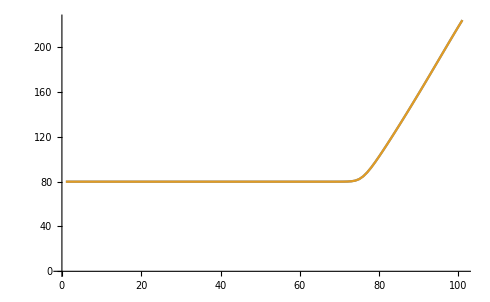

```mathematica
ListLinePlot[{externalData[[All,3]],hardNewton[[All]]}]
```

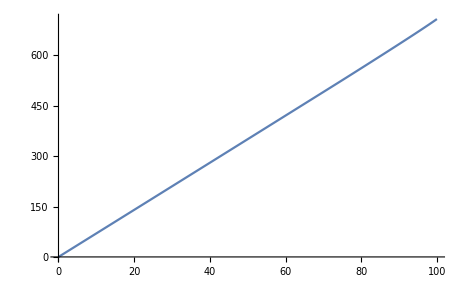

```mathematica
plotData = Table[0*i*j,{i,1,numberSteps},{j,1,2}];
plotData[[All,1]] = externalData[[All,1]];
plotData[[All,2]] = externalData[[All,2]];
ListLinePlot[plotData]
```

```mathematica
Print[NumberForm[hardRateNewton,16]];
```

{0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.4210854715202×10^-14,4.263256414560601×10^-14,2.415845301584341×10^-13,2.415845301584341×10^-13,5.286437954055145×10^-12,2.363265139138093×10^-11,2.363265139138093×10^-11,4.362874506114167×10^-10,1.80340009592328×10^-9,7.272959123838518×10^-9,2.864176451566891×10^-8,1.102315820844524×10^-7,4.149154904098395×10^-7,1.528532052930132×10^-6,5.515048300708258×10^-6,0.00001950148966045617,0.0000676236137877595,0.0002300858356107938,0.0007685214021933007,0.002520717499081115,0.0081166337800056,0.02560715861912399,0.07861500615057082,0.2302413708518571,0.6136693516621534,1.378497406040523,2.457773914007802,3.518532758967865,4.308013014606175,4.808295513775221,5.107276222311171,5.289398862268271,5.408868968756778,5.49561633273207,5.565148177336113,5.625237763097104,5.679676270747251,5.730231677087033,5.777634129424683,5.822060573366684,5.863366100007596,5.901185645893889,5.934965789146958,5.963953589603847,5.987151597851295,6.003236605648283,6.010429127896515,6.006286406387261,5.987367499580756,5.948672472015375,5.882661602517715,5.777450407123581}

```mathematica
Test consistency of kinematics
```

consistency kinematics of Test

Uncomment lines below to test this.  This tests whether the deformation gradient is consistent with a given stress .

```mathematica
(********************************** TESTING FE BELOW **********************************)
(*FTest = {{9.999814339374051*10^-01,2.541098841762901*10^-21,-8.470329472543003*10^-21},{8.470329472543003*10^-22,9.999814339374051*10^-01,-1.694065894508601*10^-21},{1.694065894508601*10^-21,-1.694065894508601*10^-21,1.000049354067958}};

FpTest = {{1.000000000000000,0.000000000000000,0.000000000000000},{-3.113438523584564*10^-168,1.000000000000000,3.113438523584564*10^-168},{-3.113438523584564*10^-168,-1.556719261792282*10^-167,1.000000000000000}};

FeTest = FTest.Inverse[FpTest]

EeTest = 0.5*(Transpose[FeTest] . FeTest-Id3);

CauchyStressTest = {{-6.438975753179005*10^-12,2.395246486360617*10^-16,-4.791346856177338*10^-16},{2.395246486360617*10^-16,-6.438975753179005*10^-12,-2.395612495851308*10^-16},{-4.791346856177337*10^-16,-2.395612495851307*10^-16,7.200267358739795}};

JeTest = Det[FeTest];

STest = JeTest * Inverse[FeTest] . CauchyStressTest . Transpose[Inverse[FeTest]];

SAltTest= Table[i*j*0,{i,1,3},{j,1,3}];
Do[
Do[SAltTest[[i,j]] = SAltTest[[i,j]] + transformElasTensor[[i,j,k,l]]*EeTest[[k,l]],
{l,1,3},{k,1,3}],{j,1,3},{i,1,3}];

MatrixForm[(SAltTest/.parameters)-STest]

MatrixForm[STest]
MatrixForm[SAltTest/.parameters]*)

(********************************** TESTING FP BELOW **********************************)

(*DeltaT = (9.076278040238446*10^01-9.049802715775348*10^01);

FpnTest = {{9.960798537549933*10^-01,0.000000000000000,-1.038077119515019*10^-16},{-5.785007013727900*10^-16,1.000000000000002,1.596029688957223*10^-17},{4.945895739810029*10^-17,0.000000000000000,1.003935574271709}};

Lpnp1Test = {{-4.233736908964702*10^-04,0.000000000000000,-2.274114056788346*10^-17},{-2.855924047598379*10^-16,0.000000000000000,-1.469093943717859*10^-17},{1.137057028394173*10^-17,0.000000000000000,4.233736908964702*10^-04}};
(*Lpnp1Test = {{-4.233736908964702*10^-04,0.000000000000000,0.0},{0.0,0.000000000000000,0.0},{0.0,0.000000000000000,4.233736908964702*10^-04}};*)

Fpnp1Test = MatrixExp[DeltaT*Lpnp1Test]FpnTest;
Print[NumberForm[MatrixForm[Fpnp1Test],16]];*)
```